Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 7 Strategies for Generalization and Hyper-Parameter Tuning

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 6, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In this chapter, we delve into some of the most critical concepts and methodologies that form the backbone of machine learning, guiding the development of models that are not only powerful but also robust and generalizable across various scenarios. We focus on the aspects of Neural Network (NN) training that determine how effectively a model can generalize from training data to unseen data. Generalization is the ultimate test of a NN’s performance, assessing its ability to apply learned patterns to new datasets.

• We begin by addressing the fundamental challenges of overfitting and generalization. Overfitting occurs when the NN learns the details and noise in the training data to an extent that it negatively impacts the performance of NN on new data. Conversely, generalization refers to the model’s ability to apply what it has learned to unseen data. We will discuss strategies to balance this, including the importance of a robust model architecture.

• Next, we explore the bias-variance trade-off, a pivotal concept that helps in diagnosing the performance of machine learning algorithms. Bias refers to errors due to overly simplistic assumptions in the learning algorithm. Variance refers to errors from sensitivity to small fluctuations in the training set. High bias can cause a model to miss the relevant relations between features and target outputs (underfitting), whereas high variance can cause modeling the random noise in the training data (overfitting).

• To assess a model’s generalization, we will split the data into three sets: training, validation, and testing [31- 38]. The training set is used to train the model, the validation set is used to tune the model’s hyperparameters and prevent overfitting, and the test set is used to evaluate the model’s performance as it simulates real-world, unseen data.

• As we measure the success of our models, performance measures come into play. Common metrics [94-99] include accuracy, precision, recall, the F1 score for classification tasks, and mean squared error or mean absolute error for regression tasks. We will explore how these metrics can guide hyperparameter tuning.

• The practice of tuning hyperparameters is essential for optimizing model performance [100-108]. Techniques such as grid search and random search are popular methods for exploring the hyperparameter space. Grid search evaluates the model across a grid of hyperparameter combinations, while random search randomly selects combinations, offering a balance between exploration and exploitation.

• Gaussian processes (GPs) [109-126] are a probabilistic model used in machine learning to predict the distribution of possible outcomes rather than just the best estimate. GPs are particularly useful for understanding model uncertainty, which can be leveraged for Bayesian optimization (BO) in hyperparameter tuning.

• Further enhancing our toolkit for hyperparameter optimization, we will introduce tuning hyperparameters with BO. BO is a strategy for the global optimization of objective functions that are noisy, expensive to evaluate, or have no closed form. It is particularly useful for tuning hyperparameters in scenarios where evaluations are costly or time-consuming. BO uses past evaluation results to form a probabilistic model mapping hyperparameters to a probability of a score on the objective function.

• Lastly, we will discuss Acquisition Functions (ACFs). ACFs in BO are used to select the next set of hyperparameters to evaluate. Common ACFs include Expected Improvement (EI), Probability of Improvement (PI), and Upper Confidence Bound (UCB). These functions help in deciding which hyperparameter settings are likely to yield improvements over the best current observations.

In this chapter, by leveraging Mathematica’s advanced functionalities, we will explore various techniques to optimize our models and enhance their predictive capabilities. The chapter is structured into five distinct units, each designed to progressively deepen the reader’s understanding and proficiency in constructing and optimizing NNs using Mathematica. From exploring the fundamental challenges of overfitting to mastering advanced techniques like BO, this chapter provides a step-by-step guide to refining predictive models and enhancing their performance in real-world scenarios.

• UNIT 7.1: The Fundamentals of Overfitting: What It Is and Why It Happens This unit begins by addressing the fundamental concept of overfitting, a common pitfall in NN training. Through illustrative examples and Mathematica simulations, we will learn how to recognize overfitting.

• UNIT 7.2: Performance Metrics Understanding how to evaluate a NN is crucial. Performance metrics are the lens through which the effectiveness of NNs is viewed. This unit focuses on the various performance metrics available in Mathematica. For regression, common metrics include mean squared error, mean absolute error, root mean squared error, and R-squared. For classification, common metrics include accuracy, precision, recall (sensitivity), F1 score, and confusion matrix. During the training process, you can use the TrainingProgressMeasurements option in Mathematica to monitor these metrics and track the progress of your model. This provides valuable feedback on how well the model is learning and allows you to make adjustments as needed to improve its performance.

• UNIT 7.3: Gaussian Processes Implementation in Mathematica from Scratch GPs offer a robust probabilistic approach to modeling in machine learning. GPs indeed serve as a cornerstone in BO. This unit demonstrates how to implement GPs in Mathematica from scratch to provide insightful predictions and uncertainty estimations.

• UNIT 7.4: Setting Up BO in Mathematica The journey through NN optimization would be incomplete without addressing BO. BO is a powerful technique for optimizing expensive, black-box functions. With Mathematica’s BayesianMinimization and BayesianMaximization functions, we will explore how to apply this sophisticated approach to streamline the hyperparameter tuning process. Additionally, utilizing Mathematica’s GaussianProcess method, we will demonstrate how GPs can be implemented, in a simple way, to make predictive models.

• UNIT 7.5: Automated Hyperparameter Tuning with Mathematica Finally, the chapter concludes by discussing automated hyperparameter tuning techniques, harnessing Mathematica’s capabilities to simplify and accelerate the search for optimal model parameters. Techniques like grid search and random search, implemented through Mathematica’s versatile programming environment, will be showcased. Moreover, using Mathematica’s built-in functions BayesianMinimization and BayesianMaximization, we will explore how to automate the search for the best model parameters, thereby simplifying the model-building process and improving performance.

By the end of this chapter, readers will be equipped with a deep understanding and practical skills to leverage Mathematica for building and optimizing NNs, ready to tackle complex real-world data challenges.

### The Fundamentals of Overfitting: What It Is and Why It Happens

code 7.1

(* The code aims to analyze the performance of polynomial regression models in approximating a sinusoidal function with added noise. It generates a set of training data points by sampling from the sinusoidal function with random noise. Subsequently, polynomials of different degrees (0,1,3, and 9) are fitted to the training data to capture the underlying relationship between the input variable (x) and the target variable (y). The code then visualizes the training data along with the original sinusoidal function curve to understand the data distribution. Additionally, separate plots are generated for each fitted polynomial curve to assess their performance in approximating the underlying function. Through this analysis, the code aims to evaluate the trade-off between model complexity and goodness of fit, providing insights into the effectiveness of polynomial regression models for the given dataset: *)

{0.0209197,0.780035-1.68692 x,0.0221099+9.33508 x-28.6867 x^2+19.6234 x^3,0.213963+236.151 x-5876.84 x^2+57575. x^3-294786. x^4+877743. x^5-1.57544×10^6 x^6+1.67889×10^6 x^7-977501. x^8+239311. x^9}

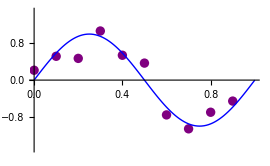

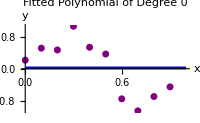
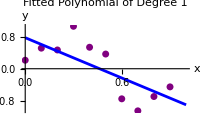
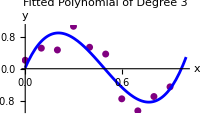
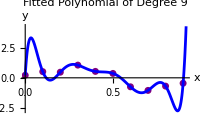

```mathematica
SeedRandom[134];
trainingData=Table[
{x,Sin[2π x]+RandomVariate[NormalDistribution[0,0.3]]},
{x,0,0.9,0.1}
];

fittedPolynomials=Table[
Fit[trainingData,Table[x^i,{i,0,m}],x],
{m,{0,1,3,9}}
]

ListPlot[
trainingData,
PlotStyle->{PointSize[0.025],Purple},
PlotRange->{{0,1},{-1.5,1.5}},
FrameLabel->{"x","y"},
AxesOrigin->{0,0},
ImageSize->270,
Epilog->{Blue,Thick,Line[Transpose[{Range[0,1,0.01],Sin[2π Range[0,1,0.01]]}]]}
]

Table[
Show[
ListPlot[
trainingData,
PlotStyle->{PointSize[0.025],Purple},
PlotRange->All,
ImageSize->200
],
Plot[
fittedPolynomials[[i]],
{x,0,1},
PlotStyle->Blue
],
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Fitted Polynomial of Degree "<>ToString[{0,1,3,9}[[i]]]
],
{i,Length[fittedPolynomials]}
]
```

code 7.2

(* The code aims to assess the performance of polynomial regression models by evaluating the root mean square (RMS) errors for varying polynomial degrees using both training and test datasets. It begins by generating a synthetic dataset composed of sinusoidal data points with added random noise. Subsequently, it defines a function to compute the residual sum of squares (RSS) to quantify the discrepancy between the fitted polynomial curves and the actual data. After generating a finer- resolution test dataset, the code fits polynomial models of increasing degrees to the training data and calculates the RMS errors for both training and test datasets. The resulting RMS error values are plotted against the polynomial degrees, providing insights into the trade-off between model complexity and generalization performance, aiding in the selection of an optimal model complexity to avoid underfitting or overfitting: *)

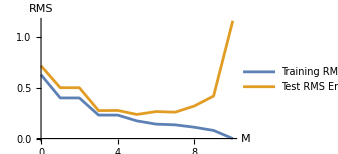

```mathematica
SeedRandom[12];
trainingData=Table[
{x,Sin[2π x]+RandomVariate[NormalDistribution[0,0.3]]},
{x,0,1,0.1}
];

calculateRSS[data_,fit_]:=Sqrt[(1/Length[data])*Total[(fit-data[[All,2]])^2]];

testData=Table[
{x,Sin[2π x]+RandomVariate[NormalDistribution[0,0.2]]},
{x,0,1,0.01}
];

orders=Range[0,10];

trainingRMS=Table[
fit=Fit[trainingData,Table[x^i,{i,0,m}],x];
fitValues=Table[fit,{x,trainingData[[All,1]]}];
calculateRSS[trainingData,fitValues],
{m,orders}
];

testRMS=Table[
fit=Fit[trainingData,Table[x^i,{i,0,m}],x];
fitValues=Table[fit,{x,testData[[All,1]]}];
calculateRSS[testData,fitValues],
{m,orders}
];

ListLinePlot[
{Transpose[{orders,trainingRMS}],Transpose[{orders,testRMS}]},
PlotLegends->{"Training RMS Error","Test RMS Error"},
AxesLabel->{"M","RMS"},
PlotRange->All,
ImageSize->250
]
```

code 7.3

(* The goal of this code is to illustrate how the behavior of fitted polynomial curves changes as the size of the dataset varies. By generating datasets of different sizes and fitting polynomial curves of the same degree to each dataset, the code aims to demonstrate the relationship between dataset size and model complexity. Specifically, it seeks to show that as the dataset size increases, the overfitting problem becomes less severe, allowing for the fitting of more complex models without encountering significant overfitting. The code generates synthetic data points simulating a sinusoidal function with added random noise, creating two datasets with different step sizes. It then fits polynomial curves of degree 9 to each dataset and visualizes the data points alongside the corresponding fitted curves: *)

0.213963+236.151 x-5876.84 x^2+57575. x^3-294786. x^4+877743. x^5-1.57544×10^6 x^6+1.67889×10^6 x^7-977501. x^8+239311. x^9

-0.545944+14.5445 x+56.2802 x^2-1413.97 x^3+8655.16 x^4-27326.1 x^5+49215. x^6-50767.8 x^7+27871.1 x^8-6301.36 x^9

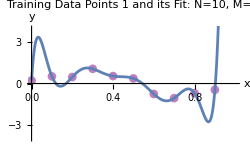

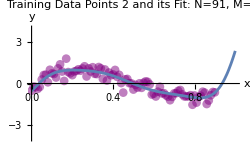

```mathematica
SeedRandom[134];
generateData[stepSize_]:=Table[
{x,Sin[2π x]+RandomVariate[NormalDistribution[0,0.3]]},
{x,0,0.9,stepSize}
]

fitPolynomial[data_,degree_]:=Fit[data,Table[x^i,{i,0,degree}],x]

plotDataAndFit[data_,fits_,label_]:=Show[
ListPlot[
data,
PlotStyle->{PointSize[0.025],Opacity[0.5],Purple},
PlotRange->All,
ImageSize->250
],
Plot[
Evaluate[fits],
{x,0,1}
],
PlotRange->{{0,1},{-4,4}},
AxesLabel->{"x","y"},
PlotLabel->label 
];

data1=generateData[0.1];
data2=generateData[0.01];

fits1=fitPolynomial[data1,9]
fits2=fitPolynomial[data2,9]

plotDataAndFit[data1,fits1,"Training Data Points 1 and its Fit: N=10, M=9"]
plotDataAndFit[data2,fits2,"Training Data Points 2 and its Fit: N=91, M=9"]
```

code 7.4

(* The code aims to analyze the performance of polynomial regression models in approximating a sinusoidal function with added noise. It begins by generating multiple training datasets with varying levels of noise, using a sinusoidal function as the underlying pattern. Then, it fits polynomials of different degrees to each dataset, allowing for exploration of the relationship between model complexity and goodness of fit. The fitted polynomials are visualized alongside the original training data, aiding in the assessment of how well the models capture the underlying sinusoidal function. Through this analysis, the code aims to provide insights into the effectiveness of polynomial regression models in capturing complex relationships while navigating the trade-off between model complexity and accuracy: *)

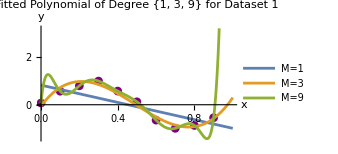
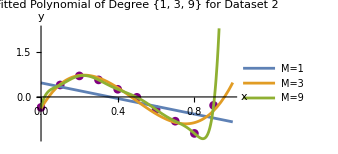
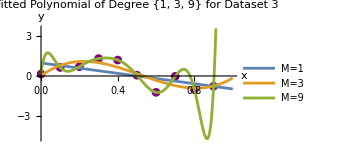
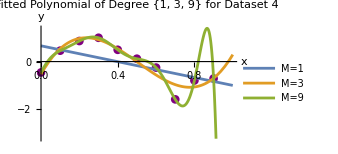

```mathematica
generateTrainingData[noise_]:=Table[
{x,Sin[2π x]+RandomVariate[NormalDistribution[0,noise]]},
{x,0,0.9,0.1}
]

fitPolynomials[data_,degrees_]:=Table[
Fit[data,Table[x^i,{i,0,m}],x],
{m,degrees}
]

plotFittedPolynomials[trainingData_,fittedPolynomials_,degrees_,dataNo_]:=Show[
ListPlot[
trainingData,
PlotStyle->{PointSize[0.025],Purple},
PlotRange->All,
ImageSize->250
],
Plot[Evaluate[fittedPolynomials],{x,0,1},
PlotLegends->Placed[{"M=1","M=3","M=9"},{0.7,0.8}]
],
PlotRange->Full,
AxesLabel->{"x","y"},
PlotLabel->"Fitted Polynomial of Degree "<>ToString[degrees]"\n for Dataset "<>ToString[dataNo]
]

SeedRandom[134];

trainingDatas=Table[generateTrainingData[i],{i,{0.1,0.2,0.3,0.4}}];

fittedPolynomials=Table[
fitPolynomials[trainingData,{1,3,9}],
{trainingData,trainingDatas}
];

plots=MapThread[
plotFittedPolynomials,
{
trainingDatas,
fittedPolynomials,
{{1,3,9},{1,3,9},{1,3,9},{1,3,9}},
{1,2,3,4}}
]
```

code 7.5

(* The code generates synthetic noisy data representing a mathematical function and trains a multilayer perceptron (MLP) neural network on this data. The MLP architecture comprises two hidden layers with 150 units each, utilizing hyperbolic tangent activation functions. Following training, the network’s performance is evaluated on a separate test dataset to assess its generalization capabilities. Despite achieving low loss on the training data, the trained model demonstrates poor performance on the test set, indicating potential overfitting. This disparity is visually demonstrated by comparing the model’s predictions to both the training and test data, highlighting the need for careful evaluation of model generalization beyond training performance: *)

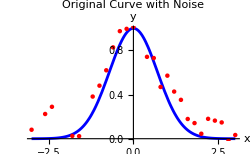

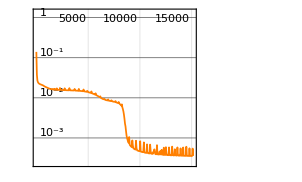
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:15138  rounds:15138  time:30s  examples/s:15675
data | ,,  training examples:31  processed examples:469278  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:3.54×10^-4
 | rounds
loss | -Graphics- | 
 | ]

0.000354046

NetChain[…]

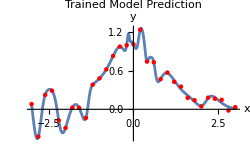

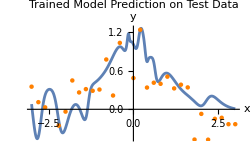

```mathematica
trainingData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],
{x,-3,3,.2}
];

trainingPlot=ListPlot[
List@@@trainingData,
PlotStyle->Red,
ImageSize->250,
AxesLabel->{"x","y"},
PlotLabel->"Trainging Data"
];

originalCurve=Plot[
Exp[-x^2],
{x,-3,3},
PlotStyle->Blue,
ImageSize->250,
AxesLabel->{"x","y"},
PlotLabel->"Original Curve with Noise"
];

Show[originalCurve,trainingPlot]

mlp=NetChain[{150,Tanh,150,Tanh,1}];

trainingResults=NetTrain[mlp,trainingData,All,TimeGoal->30]

finalLoss=trainingResults["RoundLoss"]
trainedNet=trainingResults["TrainedNet"]

predictedTrainingPlot=Plot[
trainedNet[x],
{x,-3,3},
ImageSize->250,
AxesLabel->{"x","y"},
PlotLabel->"Trained Model Prediction"
];

Show[predictedTrainingPlot,trainingPlot]

testData=Table[
x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.35]],
{x,-3,3,.2}];
testX=Keys[testData];
testY=Values[testData];

predictedTestPlot=Plot[
trainedNet[x],
{x,-3,3},
ImageSize->250,
AxesLabel->{"x","y"},
PlotLabel->"Trained Model Prediction on Test Data"
];

testPlot=ListPlot[
List@@@testData,
PlotStyle->Orange,
ImageSize->250,
AxesLabel->{"x","y"},
PlotLabel->"Test Data"
];

Show[predictedTestPlot,testPlot]
```

### Performance Metrics

In Mathematica, ValidationSet is an option used in functions like NetTrain, Predict, and Classify. It’s utilized for specifying a dataset that the neural network or machine learning model will not use for training but instead use for validation during the training process. This helps in assessing how well the model generalizes to unseen data and avoids overfitting.

TrainingProgressMeasurements is another option used in functions like NetTrain to specify what training progress metrics should be computed and returned during the training process. These metrics can include things like loss values, accuracy, etc. It allows you to monitor the progress of your training and make decisions accordingly, such as whether to stop training or adjust parameters.

NetTrainResultsObject is the output object returned by the NetTrain function in Mathematica after training a neural network. It contains various pieces of information about the training process and the trained network, such as final training and validation loss, training time, the trained neural network itself, etc. This object can be further used for evaluation, testing, or deployment of the trained model.

ValidationMeasurements is an option used in functions like Predict, Classify, and NetTrain. It allows you to specify what measurements you want to compute on the validation set during the evaluation of a trained model.

#### Validation Set

ValidationSet is an option for Predict, Classify, NetTrain, and related functions that specifies the validation set to be used during the training phase.

Remarks:

• With ValidationSet->data, model and hyperparameter selections are done by testing performance on data. data can be given in any format allowed for the training set.

• With ValidationSet->Automatic, cross-validation methods on the original data supplied to Predict, Classify, etc. will be used instead.

• ValidationSet->data is typically used when the data in the training set and the data that one wishes to predict or classify come from different sources.

• If a validation set is specified, NetTrain will return the net that produced the lowest validation loss during training with respect to this set.

The following settings for ValidationSet can be given:

None			use only the existing training set to estimate loss (default)

data			validation set in the same form as training data

Scaled[frac]		reserve a specified fraction of the training set for validation

{spec,”Interval”->int}	specify the interval at which to calculate validation loss

#### Training Progress Measurements

TrainingProgressMeasurements is an option for NetTrain that specifies measurements to make while training is in progress.

For nets that contain a CrossEntropyLossLayer, the following built-in measurements are available:

“Accuracy”		fraction of correctly classified examples

“Accuracy”->n		fraction of examples with the correct result in the top

“AreaUnderROCCurve”	area under the ROC curve for each class

“CohenKappa”		Cohen’s kappa coefficient

“ConfusionMatrix”	counts cij of class i examples classified as class j

“ConfusionMatrixPlot”	plot of the confusion matrix

“Entropy”		entropy measured in nats

“ErrorRate”		fraction of incorrectly classified examples

“ErrorRate”->n		fraction of examples with the incorrect result in the top n

“F1Score”		F1 score for each class

“FScore”->β		Fβ score for each class

“FalseDiscoveryRate”	false discovery rate for each class

“FalseNegativeNumber”number of false negative examples

“FalseNegativeRate”	false negative rate for each class

“FalseOmissionRate”	false omission rate for each class

“FalsePositiveNumber” number of false positive examples

“FalsePositiveRate”	false positive rate for each class

“Informedness”		informedness for each class

“Markedness”		markedness for each class

“MatthewsCorrelationCoefficient”	Matthews correlation coefficient for each class

“NegativePredictiveValue”		negative predictive value for each class

“Perplexity”		exponential of the entropy

“Precision”		precision for each class

“Recall”		recall rate for each class

“ROCCurve”		receiver operating characteristics (ROC) curve for each class

“ROCCurvePlot”	plot of the ROC curve

“ScottPi”		Scott’s pi coefficient

“Specificity”		specificity for each class

“TrueNegativeNumber” number of true negative examples

“TruePositiveNumber”	number of true positive examples

For nets that contain a MeanSquaredLossLayer or MeanAbsoluteLossLayer, the following built-in measurements are available:

“FractionVarianceUnexplained”the fraction of output variance left unexplained by the net

“IntersectionOverUnion”	intersection over union for bounding boxes

“MeanDeviation”		mean absolute value of the residuals

“MeanSquare”			mean square of the residuals

“RSquared”			coeficient of determination

“StandardDeviation”		root mean square of the residuals

Remarks:

• NetTrain[net,data,All] returns a NetTrainResultsObject[…] that contains values for all properties that do not require significant additional computation or memory.

• NetTrainResultsObject[…][prop] is used to look up property prop from the NetTrainResultsObject.

• Associations of the final value of all measurements can be obtained after training by specifying “RoundMeasurements” and “ValidationMeasurements” as properties in NetTrain[net,data,properties] or in a NetTrainResultsObject.

Remember, in NetTrain[net,data,prop], the property prop can be any of the following:

“BestValidationRound”	the training round corresponding to the final trained net

“ValidationExamples”		the number of examples in the validation set

“ValidationLoss”		the mean loss obtained on the ValidationSet for the most recent validation measurement

“ValidationLossList”		list of the mean losses on the ValidationSet for each validation measurement

“ValidationMeasurements”	association of training measurements on the ValidationSet after the most recent validation measurement

“ValidationMeasurementsLists” list of training measurements associations on the ValidationSet for each validation measurement

“ValidationPositions”		the batch numbers corresponding to each validation measurement

Remarks:

NetTrain[net,data,{prop1,prop2,…}] returns a list of the results for the propi.

code 7.6

(* The code is designed to create synthetic data from a Gaussian distribution, construct a neural network with two hidden layers, and train this network using the generated data with added noise. The main objectives are to accurately model the underlying data patterns, optimize the network parameters for best performance, and ensure the model’s generalization to new, unseen data through rigorous training and validation. The training process, limited to 50 rounds, includes monitoring metrics such as mean deviation, mean square error, R-squared, and standard deviation to assess accuracy and prevent overfitting, providing a comprehensive approach to training and evaluating the neural network’s performance. All the results from the training session are stored in the NetTrainResultsObject. This object provides a convenient way to access various details about the training process, including performance metrics, the best model configuration, and other properties that can help in analyzing and understanding the behavior and effectiveness of the trained neural network. You can query this object for specific details like validation losses, training metrics, and the final trained model, which are crucial for further evaluation and refinement of your model: *)

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

net=NetChain[
{
50,Tanh,
30,Tanh,
1
}
];

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"},
MaxTrainingRounds->50
]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:50  time:0.72s  examples/s:44592
data | ,,  training examples:601  validation examples:61  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.29×10^-2  res. mean dev.:1.2×10^-1  res. mean sqr.:2.29×10^-2  res. r.b2:8.41×10^-1  res. s.d.:1.51×10^-1
validation | ,,  loss:2.12×10^-2  res. mean dev.:1.19×10^-1  res. mean sqr.:2.12×10^-2  res. r.b2:8.32×10^-1  res. s.d.:1.46×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]

code 7.7

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:50  time:0.71s  examples/s:44894
data | ,,  training examples:601  validation examples:61  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.1×10^-2  res. mean dev.:1.16×10^-1  res. mean sqr.:2.1×10^-2  res. r.b2:8.48×10^-1  res. s.d.:1.45×10^-1
validation | ,,  loss:1.97×10^-2  res. mean dev.:1.12×10^-1  res. mean sqr.:1.97×10^-2  res. r.b2:8.58×10^-1  res. s.d.:1.4×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]

{ArraysLearningRateMultipliers,BatchesPerRound,BatchesPerSecond,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

NetChain[…]

47

{{47}}

Postition[{0.192149,0.15555,0.129577,0.107046,0.0923238,0.0830195,0.0750347,0.0652885,0.0563351,0.0479862,0.0416016,0.0358812,0.0319119,0.0280402,0.0257397,0.0240169,0.0230644,0.0229642,0.022056,0.0223496,0.0217453,0.0208519,0.0208066,0.0208846,0.0204541,0.0204063,0.0205597,0.0202176,0.0200597,0.0199769,0.0201024,0.0199943,0.0199082,0.0201132,0.0199292,0.020219,0.0199058,0.0201055,0.0200846,0.0197204,0.0196796,0.0198147,0.0196437,0.01973,0.019633,0.0200021,0.0195648,0.0196163,0.020009,0.0196509},0.0195648]

0.0195648

0.0195648

0.0196509

{0.0196509,0.111619,0.0196509,0.858239,0.140182}

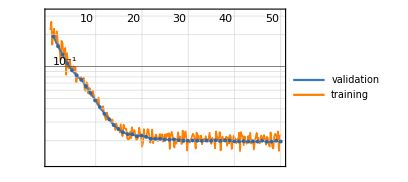
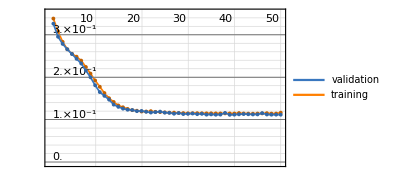
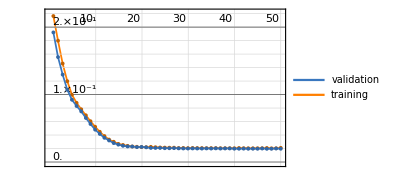
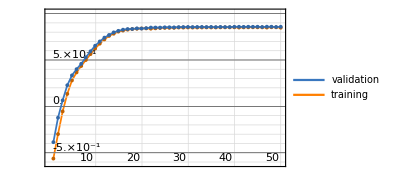
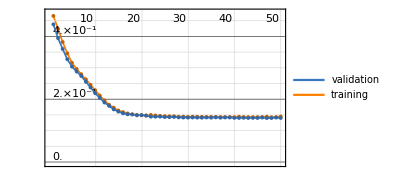
<|Loss→ | rounds
loss | -Graphics-,MeanDeviation→ | rounds
residual mean absolute | -Graphics-,MeanSquare→ | rounds
residual mean square | -Graphics-,RSquared→ | rounds
R-squared | -Graphics-,StandardDeviation→ | rounds
standard deviation | -Graphics-|>

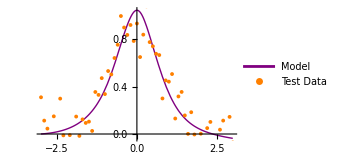

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

net=NetChain[
{
50,Tanh,
30,Tanh,
1
}
];

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"},
MaxTrainingRounds->50
]

netTrainResults["Properties"]
trainedNet=netTrainResults["TrainedNet"]
validationLossList=netTrainResults["ValidationLossList"];
validationMeasurementsLists=Values[netTrainResults["ValidationMeasurementsLists"]];

minPostion1=netTrainResults["BestValidationRound"]
minPosition2=Position[validationLossList,Min[validationLossList]]
minPosition3=Postition[validationMeasurementsLists[[1]],Min[validationMeasurementsLists[[1]]]]

minValidationLossValue1=Min[netTrainResults["ValidationLossList"]]
minValidationLossValue1=Min[netTrainResults["ValidationMeasurementsLists"][[1]]]

mostRecentValidationLoss1=netTrainResults["ValidationLoss"]

mostRecentValidationLoss1=Values[netTrainResults["ValidationMeasurements"]]
netTrainResults["FinalPlots"]

plotModel=Plot[
trainedNet[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plottestData=ListPlot[
List@@@testData,
PlotStyle->Orange,
PlotLegends->{"Test Data"}
];

Show[plotModel,plottestData,ImageSize->250]
```

code 7.8

(* This code explicitly specifies “ValidationMeasurements” as a property to retrieve in the NetTrain function. This shows a clear intent to focus on and directly access detailed validation metrics throughout the training process. This approach ensures that these specific metrics are highlighted and analyzed, which is particularly useful for a more detailed performance evaluation. Note that, the previous code does not explicitly specify a focus on validation measurements within the NetTrain function. It saves all training results in a NetTrainResultsObject, which can store a wide range of information but does not emphasize specific validation metrics unless manually accessed later: *)

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

net=NetChain[
{
50,Tanh,
30,Tanh,
1
}
];

netTrainResults=NetTrain[
net,
trainingData,
"ValidationMeasurements",
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"},
MaxTrainingRounds->50
]
```

<|Loss→0.0246182,MeanDeviation→0.122313,MeanSquare→0.0246182,RSquared→0.83754,StandardDeviation→0.156902|>

code 7.9

(* The code aims to generate a synthetic dataset within a unit disk, label the data based on proximity to the center, and visualize this distribution. It constructs a simple neural network for binary classification, which includes linear and non- linear layers to capture complex patterns. The network is trained using the generated data, validated with a separate set, and evaluated using several performance metrics. The training process is visualized through a contour plot showing the decision boundaries and other training-related plots like the confusion matrix. The goal is to demonstrate the complete workflow of data preparation, model training, and performance evaluation in a neural network application: *)

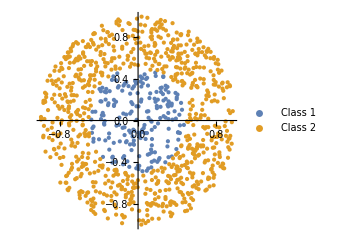

NetChain[…]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:32368  rounds:2023  time:1.4min  examples/s:25325
data | ,,  training examples:1000  validation examples:500  processed examples:2071552  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.42×10^-2  F.N.:2.  F.P.:0.  T.N.:8.14×10^2  T.P.:2.08×10^2  acc.:99.805%  F1:99.522%  M.C.C.:9.94×10^-1  prec.:100%  recall:99.048%  π:9.94×10^-1
validation | ,,  loss:3.14×10^-2  F.N.:4.  F.P.:3.  T.N.:3.65×10^2  T.P.:1.28×10^2  acc.:98.60%  F1:97.34%  M.C.C.:9.64×10^-1  prec.:97.71%  recall:96.97%  π:9.64×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]

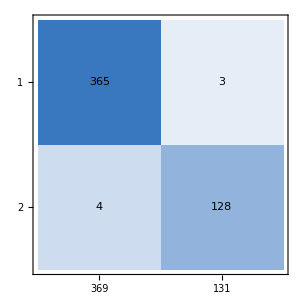
<|Loss→0.0314093,FalseNegativeNumber→4.,FalsePositiveNumber→3.,TrueNegativeNumber→365.,TruePositiveNumber→128.,Accuracy→0.986,F1Score→0.973384,MatthewsCorrelationCoefficient→0.963899,Precision→0.977099,Recall→0.969697,ScottPi→0.963886,ConfusionMatrixPlot→actual class | -Graphics-
 | predicted class|>

NetChain[…]

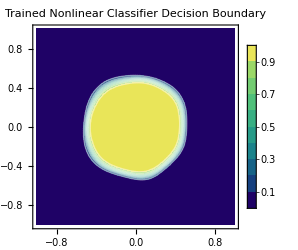

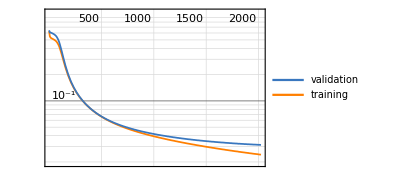
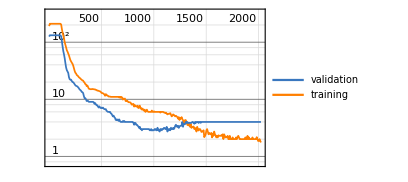
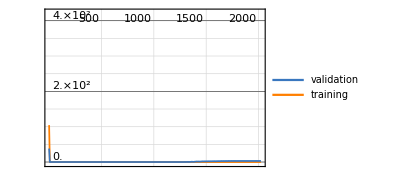
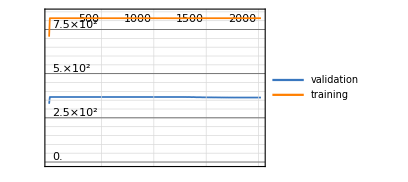
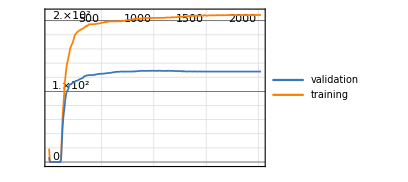
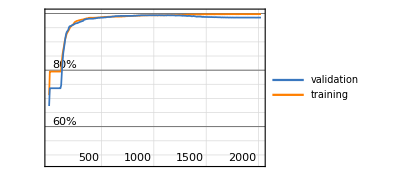
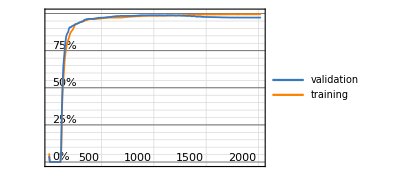
<|Loss→ | rounds
loss | -Graphics-,FalseNegativeNumber→ | rounds
false negative number | -Graphics-,FalsePositiveNumber→ | rounds
false positive number | -Graphics-,TrueNegativeNumber→ | rounds
true negative number | -Graphics-,TruePositiveNumber→ | rounds
true positive number | -Graphics-,Accuracy→ | rounds
accuracy | -Graphics-,F1Score→ | rounds
F1 score | -Graphics-,MatthewsCorrelationCoefficient→ | rounds
Matthews correlation coefficient | -Graphics-,Precision→ | rounds
precision | -Graphics-,Recall→ | rounds
recall | -Graphics-,ScottPi→ | rounds
Scott Pi | -Graphics-,ConfusionMatrixPlot→actual class | -Graphics-
 | predicted class
actual class | -Graphics-
 | predicted class|>

```mathematica
trainpoints=RandomPoint[Disk[],1000];
trainlabels=Thread[Map[Norm,trainpoints]<0.5];
trainingData=trainpoints->trainlabels;

validationPoints=RandomPoint[Disk[],500];
validattionLabels=Thread[Map[Norm,validationPoints]<0.5];
validationData=validationPoints->validattionLabels;

ListPlot[
{
Pick[trainpoints,trainlabels,True],
Pick[trainpoints,trainlabels,False]
},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},
PlotLegends->{"Class 1","Class 2"}
]

net=NetChain[
{
20,Tanh,
LinearLayer[],LogisticSigmoid},
"Output"->NetDecoder["Boolean"]
]

netTrainResults=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{
"FalseNegativeNumber","FalsePositiveNumber","TrueNegativeNumber",
"TruePositiveNumber","Accuracy","F1Score","MatthewsCorrelationCoefficient","Precision","Recall","ScottPi","ConfusionMatrixPlot"
}
]

netTrainResults["ValidationMeasurements"]
trainedNet=netTrainResults["TrainedNet"]

ContourPlot[
trainedNet[{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Trained Nonlinear Classifier Decision Boundary"]

netTrainResults["FinalPlots"]
```

code 7.10

(* The introduction of “ValidationMeasurements” in NetTrain suggests a focus on in-depth analysis and monitoring of the model’s performance specifically on the validation data throughout the training process. This can be critical for understanding how well the model generalizes to new, unseen data and for making adjustments to model parameters or training procedures based on validation feedback: *)

NetChain[…]

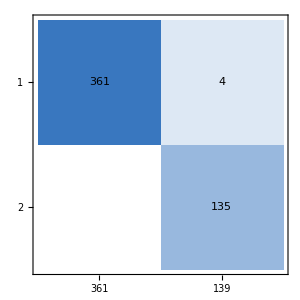
<|Loss→0.0361864,FalseNegativeNumber→0.,FalsePositiveNumber→4.,TrueNegativeNumber→361.,TruePositiveNumber→135.,Accuracy→0.992,F1Score→0.985401,MatthewsCorrelationCoefficient→0.980092,Precision→0.971223,Recall→1.,ScottPi→0.979892,ConfusionMatrixPlot→actual class | -Graphics-
 | predicted class|>

```mathematica
trainpoints=RandomPoint[Disk[],1000];
trainlabels=Thread[Map[Norm,trainpoints]<0.5];
trainingData=trainpoints->trainlabels;

validationPoints=RandomPoint[Disk[],500];
validattionLabels=Thread[Map[Norm,validationPoints]<0.5];
validationData=validationPoints->validattionLabels;

net=NetChain[
{
20,Tanh,
LinearLayer[],LogisticSigmoid},
"Output"->NetDecoder["Boolean"]
]

netTrainResults=NetTrain[
net,
trainingData,
"ValidationMeasurements",
ValidationSet->validationData,
TrainingProgressMeasurements->{
"FalseNegativeNumber","FalsePositiveNumber","TrueNegativeNumber",
"TruePositiveNumber","Accuracy","F1Score","MatthewsCorrelationCoefficient","Precision","Recall","ScottPi","ConfusionMatrixPlot"
}
]
```

### Gaussian Processes Implementation in Mathematica From Scratch

code 7.11

(* The code is a demonstration of constructing and visualizing a multivariate normal distribution. It starts by defining a zero-mean vector and a specifically structured covariance matrix to reflect varying degrees of correlation between variables. The code visualizes this matrix to elucidate the underlying correlation structure and proceeds to generate random variates, which it then plots as discrete functions. This visualization serves to both educate and illustrate the impact of covariance on the behavior of a multivariate distribution: *)

-Graphics-

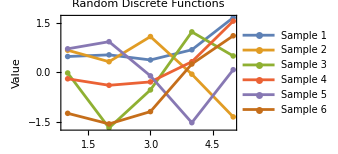

```mathematica
zeroMeanVector={0,0,0,0,0};
correaltionMatrix={
{1,0.3,0.01,0,0},{0.3,1,0.3,0.01,0},{0.01,0.3,1,0.3,0.01},{0,0.01,0.3,1,0.3},{0,0,0.01,0.3,1}
};

MatrixPlot[
correaltionMatrix,
ImageSize->250,
PlotLabel->"Covariance Matrix",
PlotLegends->Automatic,
FrameTicks->Insert[
Table[
Transpose[{Range[5],Map[Style[$,FontFamily->"Times"]&,Table[Subscript[HoldForm[y],i],{i,1,5}]]}],
2
],
None,
{{2},{2}}
]
]

multivariateDistribution=MultinormalDistribution[zeroMeanVector,correaltionMatrix];

SeedRandom[1];
randomSamples=RandomVariate[multivariateDistribution,6];

ListPlot[
Transpose[{Range[5],#}]&/@randomSamples,
Joined->True,
PlotMarkers->"OpenMarkers",
ImageSize->250,
PlotLabel->"Random Discrete Functions",
Frame->{True,True,False,False},
Axes->False,
PlotLegends->{"Sample 1","Sample 2","Sample 3","Sample 4","Sample 5","Sample 6"},
FrameLabel->{"Index","Value"}
]
```

code 7.12

(* The enhanced Mathematica code with the Manipulate function is designed to provide an interactive educational tool that allows users to dynamically explore the effects of varying correlation coefficients within a covariance matrix on a multivariate normal distribution. By enabling real-time adjustments of the correlation values and the number of samples, the tool visualizes how these changes affect the structure of the covariance matrix and the characteristics of the generated random samples. This setup not only deepens understanding of complex statistical concepts like covariance and correlation but also serves as an invaluable resource for teaching and learning about the behavior and variability of multivariate distributions, making theoretical statistics concepts tangible and visually engaging: *)

```mathematica
Manipulate[
Module[
{zeroMeanVector,correaltionMatrix,multivariateDistribution,randomSamples,matrixPlot,samplesPlot},
zeroMeanVector=ConstantArray[0,5];
correaltionMatrix=
{
{1,corr1,corr2,corr3,corr4},{corr1,1,corr1,corr2,corr3},{corr2,corr1,1,corr1,corr2},{corr3,corr2,corr1,1,corr1},{corr4,corr3,corr2,corr1,1}
};
matrixPlot=MatrixPlot[
correaltionMatrix,
ImageSize->250,
PlotLabel->"Covariance Matrix",
PlotLegends->Automatic
];
multivariateDistribution=MultinormalDistribution[zeroMeanVector,correaltionMatrix];
SeedRandom[1];
randomSamples=RandomVariate[multivariateDistribution,numSamples];
samplesPlot=ListPlot[
Transpose[{Range[5],#}]&/@randomSamples,
Joined->True,
PlotMarkers->"OpenMarkers",
ImageSize->250,
PlotLabel->"Random Discrete Functions",
Frame->{True,True,False,False},
Axes->False
];
Row[{matrixPlot,samplesPlot}]],
{{corr1,0.3,"First Correlation"},0,1,0.05},{{corr2,0.01,"Second Correlation"},0,1,0.01},{{corr3,0,"Third Correlation"},0,1,0.01},
{{corr4,0,"Fourth Correlation"},0,1,0.01},{{numSamples,6,"Number of Samples"},1,10,1}
]
```

code 7.13

(* The code demonstrates the setup and application of a Gaussian Process (GP) using a squared exponential covariance function. It calculates and visualizes a covariance matrix to illustrate the impact of point distances on their correlations, essential for understanding GP behavior. The code then generates and visualizes multiple samples from the GP, showcasing potential realizations over a defined range, thus offering insights into the variability and smoothness of the process: *)

-Graphics-

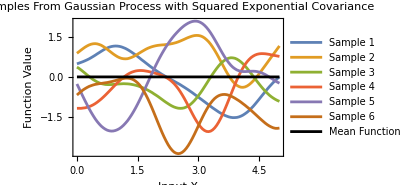

```mathematica
SquaredExponentialCovariance[x1_,x2_]:=Exp[-(x1-x2)^2];

inputPoints=Range[0,5,.05];
numberOfPoints=Length[inputPoints];

covarianceMatrix=Outer[SquaredExponentialCovariance,inputPoints,inputPoints];
covarianceMatrix=covarianceMatrix+10^-6*IdentityMatrix[numberOfPoints];

MatrixPlot[
covarianceMatrix,
ImageSize->250,
PlotLabel->"Covariance Matrix Visualization",
PlotLegends->Automatic
]

SeedRandom[1];

meanVector=ConstantArray[0,numberOfPoints];
sampledFunctions=RandomVariate[
MultinormalDistribution[meanVector,covarianceMatrix],
6
];

Show[
ListLinePlot[
Transpose[{inputPoints,#}]&/@sampledFunctions,
Axes->None,
Filling->None,
Frame->{True,True,False,False},
FrameLabel->{"Input X","Function Value"},
PlotLabel->"Samples From Gaussian Process with\n Squared Exponential Covariance",
PlotLegends->Array["Sample "<>ToString[#]&,6],
ImageSize->300
],
ListLinePlot[
Transpose[{inputPoints,meanVector}],
PlotStyle->Black,
PlotLegends->{"Mean Function"}
]
]
```

code 7.14

(* The code aims to provide an interactive and educational experience by allowing users to dynamically adjust the scale parameter and number of samples in Gaussian Process (GP). This interactivity helps illustrate how these parameters influence the covariance structure and the variability of function realizations within GP. The visualization of both covariance matrices and sampled functions facilitates a deeper understanding of key concepts like scale sensitivity and numerical stability: *)

```mathematica
Clear[CovarianceMatrix,covarianceMatrix,SquaredExponentialCovariance,VisualizeGP,matrixPlot,functionPlot];

SquaredExponentialCovariance[scale_,x1_,x2_]:=Exp[-(x1-x2)^2/scale];
inputPoints=Range[0,5,0.5];
numberOfPoints=Length[inputPoints];

CovarianceMatrix[scale_]:=Outer[SquaredExponentialCovariance[scale,#1,#2]&,inputPoints,inputPoints]+10^-6*IdentityMatrix[numberOfPoints];

meanVector=ConstantArray[0,numberOfPoints];

VisualizeGP[scale_,samples_]:=Module[
{covarianceMatrix,sampledFunctions,matrixPlot,functionPlot},
covarianceMatrix=CovarianceMatrix[scale];

sampledFunctions=RandomVariate[MultinormalDistribution[meanVector,covarianceMatrix],samples];

matrixPlot=MatrixPlot[
covarianceMatrix,
ImageSize->250,
PlotLabel->"Covariance Matrix\nScale: "<>ToString[scale],
PlotLegends->Automatic
];

functionPlot=Show[
ListLinePlot[
Transpose[{inputPoints,#}]&/@sampledFunctions,
Axes->None,
Filling->None,
Frame->{True,True,False,False},
FrameLabel->{"Input X","Function Value"},
PlotLabel->"Samples From Gaussian Process with \nSquared Exponential Covariance \nScale: "<>ToString[scale],
PlotLegends->Array["Sample "<>ToString[#]&,samples],
ImageSize->300
],
ListLinePlot[
Transpose[{inputPoints,meanVector}],
PlotStyle->Black,
PlotLegends->{"Mean Function"}
]
];
{matrixPlot,functionPlot}
];

Manipulate[
SeedRandom[1];
VisualizeGP[scale,numSamples],
{{scale,1,"Scale"},0.1,10,0.05,Appearance->"Labeled"},{{numSamples,6,"Number of Samples"},1,20,1,Appearance->"Labeled"},Initialization->{scale=1,numSamples=6}
]
```

code 7.15

```mathematica
MaternCovariance32[scale_,x1_,x2_]:=Module[{r=Abs[x1-x2]},(1+Sqrt[3]*r/scale)*Exp[-Sqrt[3]*r/scale]];

inputPoints=Range[0,5,.05];
numberOfPoints=Length[inputPoints];

CovarianceMatrix[scale_]:=Outer[MaternCovariance32[scale,#1,#2]&,inputPoints,inputPoints]+10^-6*IdentityMatrix[numberOfPoints];

SeedRandom[1];

meanVector=ConstantArray[0,numberOfPoints];

VisualizeGP[scale_,samples_]:=Module[
{covarianceMatrix,sampledFunctions,matrixPlot,functionPlot},

covarianceMatrix=CovarianceMatrix[scale];
sampledFunctions=RandomVariate[
MultinormalDistribution[meanVector,covarianceMatrix],
samples
];

matrixPlot=MatrixPlot[
covarianceMatrix,
ImageSize->250,
PlotLabel->"Covariance Matrix\nScale: "<>ToString[scale],
PlotLegends->Automatic
];

functionPlot=Show[
ListLinePlot[
Transpose[{inputPoints,#}]&/@sampledFunctions,
Axes->None,
Filling->None,
Frame->{True,True,False,False},
FrameLabel->{"Input X","Function Value"},
PlotLabel->"Samples From Gaussian Process with \nMatern Covariance (v=3/2)\nScale: "<>ToString[scale],
PlotLegends->Array["Sample "<>ToString[#]&,samples],
ImageSize->300
],
ListLinePlot[
Transpose[{inputPoints,meanVector}],
PlotStyle->Black,
PlotLegends->{"Mean Function"}
]
];
{matrixPlot,functionPlot}];

Manipulate[
SeedRandom[1];
VisualizeGP[scale,numSamples],
{{scale,0.5,"Scale"},0.1,10,0.05,Appearance->"Labeled"},
{{numSamples,6,"Number of Samples"},1,20,1,Appearance->"Labeled"},
Initialization->{scale=1,numSamples=6}
]
```

code 7.16 (Example not Working)

(* Posterior Distribution, Method 1: *)

(* The code executes Gaussian Process (GP) regression to model a sinusoidal function, generating predictions at both training and extended test input locations. It constructs covariance matrices using a squared exponential kernel, computes predictive means and covariances, and evaluates uncertainty through 95% confidence intervals. The code also simulates possible outcomes by sampling from the predictive distribution. For visualization, it plots the predictive mean, confidence intervals, actual function values, sampled paths, and training data. This visual representation helps in assessing the accuracy, reliability, and variability of the model’s predictions, demonstrating the practical application and interpretative power of GP regression in a statistical learning context: *)

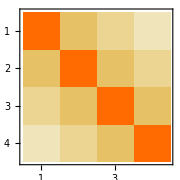

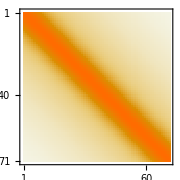

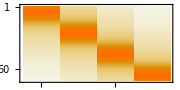

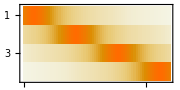

```mathematica
numTraining=4;
trainingInputs=Transpose[{Subdivide[0,2π,numTraining-1]}];
trainingOutputs=Sin[trainingInputs];
trainingDistMatrix=Outer[EuclideanDistance,trainingInputs,trainingInputs,1]^2;

stabilityEpsilon=10.^-6;

covarianceMatrixTraining=Exp[-trainingDistMatrix]+DiagonalMatrix[ConstantArray[stabilityEpsilon,numTraining]];

MatrixPlot[
covarianceMatrixTraining,
ImageSize->Small
]

testInputs=Transpose[{Subdivide[-0.5,2π+0.5,70]}];
testDistMatrix=Outer[EuclideanDistance,testInputs,testInputs,1]^2;

covarianceMatrixTest=Exp[-testDistMatrix]+DiagonalMatrix[ConstantArray[stabilityEpsilon,Length[testInputs]]];

MatrixPlot[
covarianceMatrixTest,
ImageSize->Small
]

crossDistMatrix=Outer[EuclideanDistance,testInputs,trainingInputs,1]^2;
crossCovarianceMatrix=Exp[-crossDistMatrix];

MatrixPlot[
crossCovarianceMatrix,
ImageSize->Small,
AspectRatio->1/2
]

MatrixPlot[
Transpose[crossCovarianceMatrix],
ImageSize->Small,
AspectRatio->1/2
]

inverseCovarianceMatrix=Inverse[covarianceMatrixTraining];
predictiveMean=crossCovarianceMatrix.inverseCovarianceMatrix.trainingOutputs;

predictiveCovariance=covarianceMatrixTest-crossCovarianceMatrix.inverseCovarianceMatrix.Transpose[crossCovarianceMatrix];

confidenceLower=predictiveMean+Quantile[NormalDistribution[0,1],0.05]Sqrt[Diagonal[predictiveCovariance]];
confidenceUpper=predictiveMean+Quantile[NormalDistribution[0,1],0.95]Sqrt[Diagonal[predictiveCovariance]];

sampledPredictions=RandomVariate[
MultinormalDistribution[
Flatten[predictiveMean],
predictiveCovariance
],
6
];

Show[
ListLinePlot[
Join[
{
Transpose[{Flatten[testInputs],Flatten[predictiveMean]}],
Transpose[{Flatten[testInputs],Flatten[Sin[testInputs]]}]
},
Table[
Transpose[{Flatten[testInputs],sampledPredictions[[i]]}],
{i,1,5}
],
{
Transpose[{Flatten[testInputs],Flatten[confidenceLower]}],
Transpose[{Flatten[testInputs],Flatten[confidenceUpper]}]
}
],
PlotStyle->Join[
{Blue,{Thick,Black}},
Table[Automatic,{5}],
{
{Thickness[0.003],Red,Dashed},
{Thickness[0.003],Red,Dashed}
}
],
AxesLabel->{"x","y"},
PlotRange->Full,
PlotLegends->Join[
{"Predictive Mean","True Function"},
Table["Sampled Path "<>ToString[i],{i,1,5}],
{"Lower 95% Confidence Interval","Upper 95% Confidence Interval"}
]
],
ListPlot[
Transpose[{Flatten[trainingInputs],Flatten[trainingOutputs]}],
PlotMarkers->{"OpenMarkers",10},
PlotStyle->Black,
PlotLegends->{"Training Data"}
],
ImageSize->300
]
```

code 7.17

(* The code serves as a comprehensive demonstration of a Gaussian Process (GP) modeled with a squared exponential kernel, specifically focusing on the process’s behavior when conditioned on a single training data point. It starts by defining the covariance function and generating a grid of evaluation points, followed by the computation of the initial covariance matrix which is then adjusted based on the known training data to reflect updated beliefs about correlations within the process. This adjustment, illustrated through MatrixPlot, highlights the impact of the training data on the GP’s covariance structure. The code further computes the predictive mean based on the conditioned covariance and samples multiple function realizations from this distribution, showcasing the variability and potential shapes of the GP consistent with the observed data. These steps are visualized in a comprehensive plot that combines the sampled functions, predictive mean, and training data, providing a clear visual representation of the Gaussian Process methodology and its application in probabilistic modeling and Bayesian inference: *)

-Graphics-

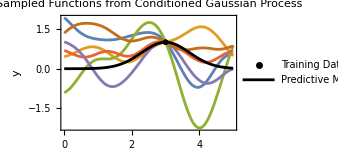

```mathematica
SquaredExponentialKernel[x1_,x2_]:=Exp[-(x1-x2)^2];
evaluationPoints=Range[0,5,0.05];
totalPoints=Length[evaluationPoints];

initialCovariance=Outer[SquaredExponentialKernel,evaluationPoints,evaluationPoints];
stabilizedCovariance=initialCovariance+10^-6*IdentityMatrix[totalPoints];

trainingInput={3.};
trainingOutput={1};
trainingIndex=Nearest[evaluationPoints->"Index",trainingInput][[All,1]];

conditionedCovariance=stabilizedCovariance-stabilizedCovariance[[All,trainingIndex]].Inverse[stabilizedCovariance[[trainingIndex,trainingIndex]]].stabilizedCovariance[[trainingIndex,All]];
conditionedCovariance=conditionedCovariance+10^-6*IdentityMatrix[totalPoints];

MatrixPlot[
conditionedCovariance,
ImageSize->250,
PlotLabel->"Conditioned Covariance Matrix",
PlotLegends->Automatic
]

predictiveMean=initialCovariance[[All,trainingIndex]].Inverse[initialCovariance[[trainingIndex,trainingIndex]]].trainingOutput;

SeedRandom[12];
SampledSoundFunctions=RandomVariate[
MultinormalDistribution[predictiveMean,conditionedCovariance],
6
];

Show[
ListPlot[
Map[Transpose[{evaluationPoints,#}]&,SampledSoundFunctions],
Joined->True,
Axes->None,
Frame->{True,True,False,False},
FrameLabel->{"x","y"},
PlotLabel->"Sampled Functions from Conditioned\n Gaussian Process",
ImageSize->250
],
ListPlot[
Transpose[{Part[evaluationPoints,trainingIndex],trainingOutput}],
PlotMarkers->"OpenMarkers",
PlotStyle->Black,
PlotLegends->{"Training Data"},
ImageSize->250
],
ListLinePlot[
Transpose[{evaluationPoints,predictiveMean}],
PlotStyle->Directive[GrayLevel[0],Opacity[1]],
PlotLegends->{"Predictive Mean"},
ImageSize->250
]
]
```

code 7.18

(* The code utilizes the Manipulate function to create an interactive visualization for exploring Gaussian Processes (GPs) conditioned on training data. It starts by defining a squared exponential kernel for covariance, generates a set of evaluation points, and computes an initial covariance matrix. This matrix is stabilized and then adjusted based on user-provided training data. The code visualizes the resulting conditioned covariance matrix, computes the predictive mean, and generates multiple potential function realizations. These components are visualized together, demonstrating the influence of training data on GP behavior and prediction variability. The interactive controls allow users to manipulate training data and the number of samples to see their effect on the Gaussian Process outcomes: *)

```mathematica
Manipulate[
SquaredExponentialKernel[x1_,x2_]:=Exp[-(x1-x2)^2];
evaluationPoints=Range[0,5,0.05];
totalPoints=Length[evaluationPoints];

initialCovariance=Outer[SquaredExponentialKernel,evaluationPoints,evaluationPoints];
stabilizedCovariance=initialCovariance+10^-6*IdentityMatrix[totalPoints];
trainingIndex=Nearest[evaluationPoints->"Index",{trainingInput}][[All,1]];

conditionedCovariance=stabilizedCovariance-stabilizedCovariance[[All,trainingIndex]].Inverse[stabilizedCovariance[[trainingIndex,trainingIndex]]].stabilizedCovariance[[trainingIndex,All]];
conditionedCovariance=conditionedCovariance+10^-6*IdentityMatrix[totalPoints];

matrixPlot=MatrixPlot[conditionedCovariance,ImageSize->250,PlotLabel->"Conditioned Covariance Matrix",PlotLegends->Automatic];

predictiveMean=initialCovariance[[All,trainingIndex]].Inverse[initialCovariance[[trainingIndex,trainingIndex]]].{trainingOutput};

SeedRandom[12];
sampledFunctions=RandomVariate[MultinormalDistribution[Flatten[predictiveMean],conditionedCovariance],numSamples];

functionsPlot=Show[ListPlot[Map[Transpose[{evaluationPoints,#}]&,sampledFunctions],Joined->True,Axes->None,Frame->{True,True,False,False},FrameLabel->{"x","y"},PlotLabel->"Sampled Functions from Conditioned\n Gaussian Process",ImageSize->250],ListPlot[Transpose[{Part[evaluationPoints,trainingIndex],{trainingOutput}}],PlotMarkers->"OpenMarkers",PlotStyle->Black,PlotLegends->{"Training Data"},ImageSize->250],
ListLinePlot[Transpose[{evaluationPoints,predictiveMean}],PlotStyle->Directive[GrayLevel[0],Opacity[1]],PlotLegends->{"Predictive Mean"},ImageSize->250]
];
{matrixPlot,functionsPlot},
{{trainingInput,3,"trainingInput"},1,5,0.1,Appearance->"Labeled"},{{trainingOutput,1,"trainingOutput"},0.5,5,0.1,Appearance->"Labeled"},{{numSamples,6,"Number of Samples"},1,20,1,Appearance->"Labeled"},Initialization->{trainingInput=3,trainingOutput=1}
]
```

code 7.19

(* The code is designed to demonstrate the principles of Gaussian Processes (GPs) conditioned on training data, illustrating how known observations influence the mean and covariance structure of the GP. The main goals are to visually represent the effect of conditioning on the covariance matrix, generate and display multiple function realizations from the conditioned GP, and serve as an educational tool for understanding the dynamics of GPs: *)

-Graphics-

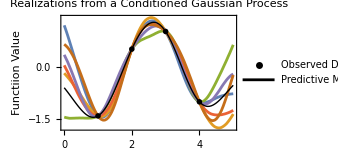

```mathematica
SquaredExponential[x1_,x2_]:=Exp[-(x1-x2)^2];
evaluationPoints=Range[0,5,0.05];
numPoints=Length[evaluationPoints];

initialCovariance=Outer[SquaredExponential,evaluationPoints,evaluationPoints];
stabilizedCovariance=initialCovariance+10^-6*IdentityMatrix[numPoints];

trainingInputs={2.,4.,1.,3.};
trainingOutputs={0.5,-1.,-1.4,1};
trainingIndices=Flatten[Nearest[evaluationPoints->"Index",trainingInputs]];

conditionedCovariance=stabilizedCovariance-Dot[Part[stabilizedCovariance,All,trainingIndices],Inverse[Part[stabilizedCovariance,trainingIndices,trainingIndices]],Part[stabilizedCovariance,trainingIndices,All]];
conditionedCovariance=conditionedCovariance+IdentityMatrix[numPoints]/10^6;

MatrixPlot[
conditionedCovariance,
ImageSize->250,
PlotLabel->"Conditioned Covariance Matrix",
PlotLegends->Automatic
]

conditionalMean=stabilizedCovariance[[All,trainingIndices]].Inverse[stabilizedCovariance[[trainingIndices,trainingIndices]]].trainingOutputs;

SeedRandom[12];
sampledPaths=RandomVariate[
MultinormalDistribution[conditionalMean,conditionedCovariance],
6
];

Show[
ListPlot[
Map[Transpose[{evaluationPoints,#}]&,sampledPaths],
Joined->True,
Axes->None,
Filling->None,
Frame->{True,True,False,False},
FrameLabel->{"Input Position","Functiion Value"},
PlotLabel->"Realizations from a Conditioned \n Gaussian Process",
ImageSize->250
],
ListPlot[
Transpose[{evaluationPoints[[trainingIndices]],trainingOutputs}],
PlotMarkers->"OpenMarkers",
PlotStyle->Black,
PlotLegends->{"Observed Data"},
ImageSize->250
],
ListLinePlot[
Transpose[{evaluationPoints,conditionalMean}],
PlotStyle->Directive[Black,Thick],
PlotLegends->{"Predictive Mean"},
ImageSize->250
]
]
```

### Setting Up Bayesian Optimization in Mathematica

Bayesian optimization is a powerful strategy for the optimization of objective functions that are expensive to evaluate. It is particularly useful in scenarios where acquiring new data points is costly or experiments take a long time. This unit provides a practical guide to implementing Bayesian optimization in Mathematica using several of its built-in functions: Predict, GaussianProcess, BayesianMinimization, and BayesianMaximization.

• The Predict function in Mathematica is a high-level machine learning function used to create predictive models from data. It automatically selects the appropriate machine learning algorithm based on the nature of the data provided. This function can handle various types of data, including numeric, categorical, and textual data, making it versatile for a range of predictive tasks. Once trained, the model can be used to make predictions on new data. It supports different prediction methods like linear regression, decision trees, neural networks, and more, depending on the structure and complexity of the data.

• In Mathematica, GaussianProcess can indeed be used as a method within the Predict function. This approach allows you to utilize Gaussian process models for predictive tasks.

• BayesianMinimization is a function in Mathematica that applies Bayesian optimization techniques to find the minimum of a function. This method is useful for optimization problems where evaluations of the function are costly or time-consuming. Bayesian optimization uses a probabilistic model to predict the function’s behavior and makes decisions based on these predictions to sample the most promising areas. It is particularly effective for optimizing hyperparameters in machine learning models or any scenario where the objective function does not have a simple analytical form and requires expensive evaluations.

• BayesianMaximization is similar to BayesianMinimization but focuses on finding the maximum value of a function. Like its minimization counterpart, it uses Bayesian optimization strategies to intelligently explore the function space, balancing the exploration of new areas with the exploitation of known good areas. This function is particularly useful when dealing with complex optimization landscapes that are difficult to navigate with traditional methods due to multiple local maxima or the expensive nature of function evaluations.

These functions represent a powerful suite of tools in Mathematica for handling various types of data analysis, predictive modeling, and optimization tasks, each equipped with sophisticated algorithms and easy-to-use interfaces to cater to both novice users and expert analysts.

#### Predict

Predict[{in1->out1,in2->out2,…}] generates a PredictorFunction[…] based on the example input-output pairs given.

Predict[{in1,in2,…}->{out1,out2,…}] generates the same result.

Predict[training,input] attempts to predict the output associated with input from the training examples given.

Predict[“name”,input] uses the built-in predictor function represented by “name”.

Predict[predictor,opts] takes an existing predictor function and modifies it with the new options given.

#### GaussianProcess

GaussianProcess Method for Predict.

Predict[data, Method->”GaussianProcess”] Infers values by conditioning a Gaussian process on the training data.

The following options can be given:

AssumeDeterministic	False			whether or not the function should be assumed to be deterministic

“CovarianceType”	Automatic 		the covariance type to use

“EstimationMethod”	“MaximumPosterior” 	the method to infer the values

“OptimizationMethod”	Automatic 		the optimization method to estimate parameters

Possible settings for “CovarianceType” include:

“SquaredExponential”	exponential kernel

“HammingDistance”	exponential kernel for nominal variables

“Periodic”		periodic kernel

“RationalQuadratic”	rational quadratic kernel

“Linear”		linear kernel

“Matern5/2”		Matérn kernel with exponent 5/2

“Matern3/2”		Matérn kernel with exponent 3/2

“Composite”		a composition of the previous kernels

assoc			specify a different kernel for each feature type

Possible settings for “EstimationMethod” include:

“MaximumPosterior”		maximize the posterior distribution

“MaximumLikelihood”	maximize the likelihood

“MeanPosterior”		mean of the posterior distribution

Possible settings for “OptimizationMethod” include:

“SimulatedAnnealing”		uses simulated annealing to find the minimum

“FindMinimum”		uses FindMinimum to find the minimum

#### BayesianMinimization/BayesianMaximazation

BayesianMinimization [f,{conf1,conf2,…}] gives an object representing the result of Bayesian minimization of the function f over the configurations confi.

BayesianMinimization[f,reg] minimizes over the region represented by the region specification reg.

BayesianMinimization[f,sampler] minimizes over configurations obtained by applying the function sampler.

BayesianMinimization [f,{conf1,conf2,…}->nsampler] applies the function nsampler to successively generate configurations starting from the confi.

BayesianMaximization[f,{conf1,conf2,…}] gives an object representing the result of Bayesian maximization over the function f over the configurations confi.

BayesianMaximization[f,reg] maximizes over the region represented by the region specification reg.

BayesianMaximization[f,sampler] maximizes over configurations obtained by applying the function sampler.

BayesianMaximization[f,{conf1,conf2,…}->nsampler] applies the function nsampler to successively generate configurations starting from the confi.

Remarks:

• BayesianMinimization[…] returns a BayesianMinimizationObject[…] whose properties can be obtained using BayesianMinimizationObject[…][“prop”].

• BayesianMinimizationObject[…][{prop1,prop2, …}] gives the list of properties {prop1,prop2,…}.

• BayesianMaximization[…] returns a BayesianMaximizationObject[…] whose properties can be obtained using BayesianMaximizationObject[…][“prop”].

• BayesianMaximizationObject[…][{prop1,prop2,…}] gives the list of properties {prop1,prop2,…}.

• Configurations can be of any form accepted by Predict (single data element, list of data elements, association of data elements, etc.) and of any type accepted by Predict (numerical, textual, sounds, images, etc.).

Possible properties include:

“EvaluationHistory”	configurations and values explored during minimization/maximization

“MinimumConfiguration”/”MaximumConfiguration” configuration found that minimizes/maximizes the result from f

“MinimumValue”/”MaximumValue” estimated minimum/maximum value obtained from f

“Method”		method used for Bayesian maximization

“NextConfiguration”	configuration to sample next if maximization were continued

“PredictorFunction”	best prediction model found for the function f

“Properties”		list of all available properties

BayesianMinimization/BayesianMaximization takes the following options:

AssumeDeterministic	False		whether to assume that f is deterministic

InitialEvaluationHistoryNone		initial set of configurations and values

MaxIterations		100		maximum number of iterations

Method			Automatic	method used to determine configurations to evaluate

RandomSeeding	1234		what seeding of pseudorandom generators should be done internally

Possible settings for Method include:

Automatic			automatically choose the method

“MaxExpectedImprovement”	maximize expected improvement over current best value

“MaxImprovementProbability”	maximize improvement probability over current best value

code 7.20

(* The code showcases the versatility of the Predict function by demonstrating its usage with diverse types of training data. Each example employs a distinct format of training data, including single-input rules, multi-feature examples, input- output lists, and nominal value mappings, illustrating the function’s adaptability to different data structures: *)

```mathematica
predictiorWithSingleInput=Predict[{10->3.5,20->7.2,30->10.8,40->14.1,50->18.2}]

predictiorWithSingleInput[15]

predictorWIthMultipleInputs=Predict[{{-0.3,0.8}->2.1,{0.1,-0.5}->3.2,{-0.5,-0.2}->1.5,{0.2,0.3}->4.0,{0.5,-0.1}->4.7}]
predictorWIthMultipleInputs[{0.1,-0.3}]

predictorWithInputList=Predict[{10,20,30,40,50}->{3.5,7.2,10.8,14.1,18.2}]
predictorWithInputList[45]

nomialPredictor=Predict[{"C"->6.3,"D"->7.8,"C"->8.1,"D"->9.5,"D"->10.2}]
nomialPredictor["D"]
```

PredictorFunction[…]

5.29172

PredictorFunction[…]

3.36946

PredictorFunction[…]

16.2084

PredictorFunction[…]

9.

code 7.21

(* The code demonstrates Gaussian Process (GP) regression, a method well-suited for predictive modeling with limited data, particularly for quantifying uncertainty in predictions. The code trains a GP model on a small dataset, retrieves detailed model information, and visualizes the probability density functions (PDFs) to analyze predictive distributions at specific and varied input values. It further assesses model accuracy and reliability by comparing predicted means and confidence intervals against actual data: *)

Predictor information
Data type | Numerical
Method | GaussianProcess
Single evaluation time | 1.86 ms/example
Batch evaluation speed | 95.2 examples/ms
Model memory | 121. kB
Training examples used | 4 examples
Training time | 141. ms

NormalDistribution[1.51826,0.113466]

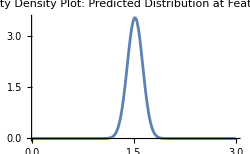

General::munfl: Exp[-896.283] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3762.15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-761.301] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

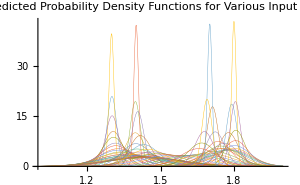

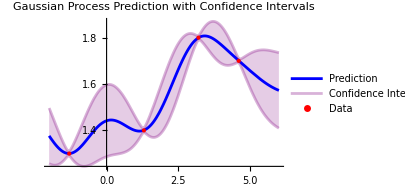

```mathematica
trainingData={-1.3->1.3,1.3->1.4,3.2->1.8,4.6->1.7};
predictor=Predict[trainingData,Method->"GaussianProcess"];

Information[predictor]

predictedDistribution=predictor[2,"Distribution"]

Plot[
PDF[predictedDistribution,y],
{y,0,3},
PlotRange->Full,
ImageSize->250,
FrameLabel->{"Value","Probability Density"},
PlotLabel->"Probability Density Plot: \n Predicted Distribution at Feature Value 2"]

pdfs=Table[
PDF[predictor[i,"Distribution"],y],
{i,-2,5,0.1}
];

Plot[
pdfs,
{y,1,2},
PlotRange->Full,
ImageSize->300,
PlotStyle->{Thickness[0.001]},
FrameLabel->{"Value","Probability Density"},
PlotLabel->"Predicted Probability Density Functions\n for Various Input Values "]

Show[
Plot[
{
predictor[x],
predictor[x]+StandardDeviation[predictor[x,"Distribution"]],
predictor[x]-StandardDeviation[predictor[x,"Distribution"]]
},
{x,-2,6},
PlotStyle->{Blue,{Opacity[0.3],Purple},{Opacity[0.3],Purple}},
Filling->{2->{3}},
FillingStyle->{Opacity[0.001],BLue},
Exclusions->False,
ImageSize->300,
PerformanceGoal->"Speed",
PlotLegends->{"Prediction","Confidence Interval"},
PlotLabel->"Gaussian Process Prediction with Confidence Intervals"
],
ListPlot[
List@@@trainingData,
PlotStyle->{Red,PointSize[Large]},
PlotLegends->{"Data"}
]
]
```

code 7.22

(* Above Code: Visualizes the predicted mean along with upper and lower confidence bounds based on standard deviation. This Code: Uses quantiles to determine and plot confidence intervals, explicitly calculating them based on a defined confidence level (e.g., 95%), providing a more customized view of uncertainty: *)

6.00389

NormalDistribution[6.00389,0.707892]

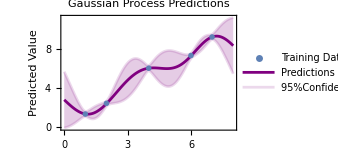

```mathematica
dataset={1->1.3,2->2.4,4->6,6->7.3,7->9.2};

predictiveModel=Predict[
dataset,
Method->"GaussianProcess"
];

predictedValue=predictiveModel[4.5]
predictionDistribution=predictiveModel[4.5,"Distribution"]

confidenceLevel=0.95;

Show[
Plot[
{
predictiveModel[x],
Quantile[predictiveModel[x,"Distribution"],(1+confidenceLevel)/2],
Quantile[predictiveModel[x,"Distribution"],(1-confidenceLevel)/2]
},
{x,0,8},
PlotStyle->{Purple,{Opacity[0.15],Purple},{Opacity[0.15],Purple}},
Filling->{2->{3}},
FillingStyle->{Opacity[0.001],Purple},
Exclusions->False,
FrameLabel->{"Input","Predicted Value"},
PlotLabel->"Gaussian Process Predictions",
PlotLegends->{"Predictions",ToString[Round[100 confidenceLevel]]<>"%Confidence Interval"},
Frame->{True,True,False,False},
FrameTicksStyle->Thin,
ImageSize->250,
PerformanceGoal->"Speed"
],
ListPlot[
Apply[List,dataset,{1}],
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[{"Training Data"},{0.75,0.2}]
]
]
```

code 7.23

(* The code aims to generate a synthetic dataset, train multiple Gaussian Process regression models using various covariance functions, and visualize their predictions alongside confidence intervals. It creates a dataset by mapping values from -10 to 10 to a noisy sine function, trains models with covariance functions such as Squared Exponential, Periodic, Rational Quadratic, Matern 5/2, and Matern 3/2, and predicts over the same range. Each model’s predictions and 95% confidence intervals are plotted against the actual sine function and the original data points for comparison, allowing an analysis of how different covariance functions affect the model’s predictive accuracy and uncertainty estimation: *)

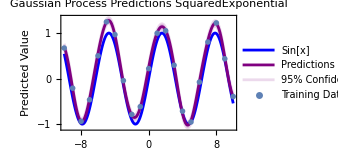
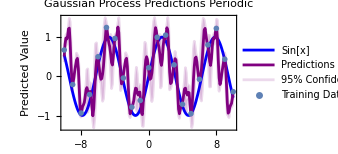
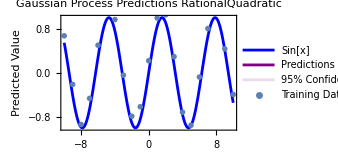
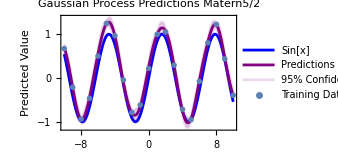
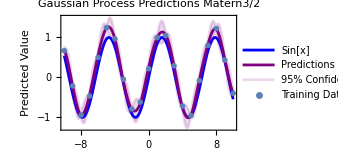

```mathematica
dataset=Table[x->Sin[x]+RandomReal[0.3],{x,-10,10,1}];

{predictorSE,predictorPeriodic,predictorRQ,predictorMatern52,predictorMatern32}=Predict[
dataset,
Method->{"GaussianProcess","CovarianceType"->#}]&/@{
"SquaredExponential",
"Periodic",
"RationalQuadratic",
"Matern5/2",
"Matern3/2"
};

confidenceLevel=0.95;

Table[Show[
Plot[
{Sin[x],
predictiveModel[[1]][x],
Quantile[predictiveModel[[1]][x,"Distribution"],(1+confidenceLevel)/2],
Quantile[predictiveModel[[1]][x,"Distribution"],(1-confidenceLevel)/2]
},
{x,-10,10},
PlotStyle->{Blue,Purple,{Opacity[0.15],Purple},{Opacity[0.15],Purple}},
Filling->{3->{4}},
FillingStyle->{Opacity[0.001],Purple},
Exclusions->False,
FrameLabel->{"Input","Predicted Value"},
PlotLabel->"Gaussian Process Predictions\n"<>predictiveModel[[2]],
PlotLegends->{"Sin[x]","Predictions",ToString[Round[100 confidenceLevel]]<>"% Confidence Interval"},
Frame->{True,True,False,False},
FrameTicksStyle->Thin,
FrameStyle->Thin,
ImageSize->250,
PerformanceGoal->"Speed"
],
ListPlot[
Apply[List,dataset,{1}],
PlotMarkers->"OpenMarkers",
PlotLegends->{"Training Data"}
]
],{predictiveModel,{
{predictorSE,"SquaredExponential"},
{predictorPeriodic,"Periodic"},
{predicorRQ,"RationalQuadratic"},
{predictorMatern52,"Matern5/2"},
{predictorMatern32,"Matern3/2"}}}]
```

code 7.24

(* The code demonstrates Bayesian optimization to find the maximum of a complex function, sin(3x)⋅Exp[−0.3 x], across an interval [0,10]. This function, characterized by its oscillatory and decaying nature, poses a significant challenge due to multiple local maxima. The code efficiently identifies the optimal input configuration and the corresponding maximum function value, showcasing Bayesian optimization’s ability to navigate complex landscapes. Additionally, it visualizes the function and the optimization outcome, enhancing the understanding of the process and its effectiveness: *)

BayesianMaximizationObject[…]

0.498886

0.857322

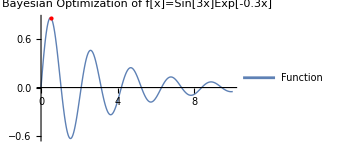

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x]
optimizationResult=BayesianMaximization[objectiveFunction,Interval[{0,10}]]
optimalConfiguration=optimizationResult["MaximumConfiguration"]
optimalFunctionValue=optimizationResult["MaximumValue"]

Plot[
Sin[3x]Exp[-0.3x],
{x,0,10},
PlotStyle->Thick,
PlotRange->All,
Epilog->{
Red,
PointSize[Large],
Point[{optimalConfiguration,optimalFunctionValue}]
},
PlotLegends->Placed[{"Function"},{0.8,0.8}],
PlotLabel->"Bayesian Optimization of\n f[x]=Sin[3x]Exp[-0.3x]",
ImageSize->250
]
```

code 7.25

(* The code utilizes Bayesian optimization to find the maximum value of the function f(x)=sin(3x)⋅Exp[−0.3 x] within a specified interval. By performing Bayesian optimization on the function, it identifies the input configuration (x-value) from a predefined set where the function is estimated to reach its maximum. Small differences in the initial configurations lead to variations in the estimated maximum value. The code then generates a plot that visually represents the function over a defined range of x-values and marks the point of maximum with a red dot: *)

BayesianMaximizationObject[…]

2.3

0.282686

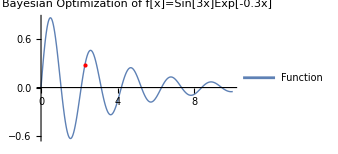

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x]
optimizationResult=BayesianMaximization[objectiveFunction,{5.7,1.1,3.4,6.8,2.3,1.2}]
optimalConfiguration=optimizationResult["MaximumConfiguration"]
optimalFunctionValue=optimizationResult["MaximumValue"]

Plot[
Sin[3x]Exp[-0.3x],
{x,0,10},
PlotStyle->Thick,
PlotRange->All,
Epilog->{
Red,
PointSize[Large],
Point[{optimalConfiguration,optimalFunctionValue}]
},
PlotLegends->Placed[{"Function"},{0.8,0.8}],
PlotLabel->"Bayesian Optimization of\n f[x]=Sin[3x]Exp[-0.3x]",
ImageSize->250
]
```

code 7.26

(* Small differences in the initial configurations lead to variations in the estimated maximum value. In this case we use Table[RandomReal[{5,10}],10]: *)

BayesianMaximizationObject[…]

8.86505

0.0696497

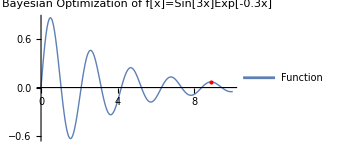

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x]
optimizationResult=BayesianMaximization[objectiveFunction,Table[RandomReal[{5,10}],10]]
optimalConfiguration=optimizationResult["MaximumConfiguration"]
optimalFunctionValue=optimizationResult["MaximumValue"]

Plot[
Sin[3x]Exp[-0.3x],
{x,0,10},
PlotStyle->Thick,
PlotRange->All,
Epilog->{
Red,
PointSize[Large],
Point[{optimalConfiguration,optimalFunctionValue}]
},
PlotLegends->Placed[{"Function"},{0.8,0.8}],
PlotLabel->"Bayesian Optimization of\n f[x]=Sin[3x]Exp[-0.3x]",
ImageSize->250
]
```

code 7.27

(* The code aims to minimize the function f(x)=sin(3x)⋅Exp[−0.3 x] using Bayesian optimization within the interval [0,20]. By defining the objective function and applying Bayesian minimization, the code seeks to identify the input configuration that results in the lowest function value. After the optimization process, it retrieves the configuration and the corresponding minimum function value. The code then generates a plot of the function over the interval [0,20] and marks the minimum point with a red dot, providing a visual representation of the optimization outcome: *)

BayesianMinimizationObject[…]

1.72447

-0.571418

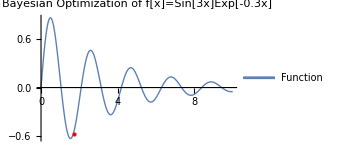

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x]
optimizationResult=BayesianMinimization[objectiveFunction,Interval[{0,20}]]
optimalConfiguration=optimizationResult["MinimumConfiguration"]
optimalFunctionValue=optimizationResult["MinimumValue"]

Plot[
Sin[3x]Exp[-0.3x],
{x,0,10},
PlotStyle->Thick,
PlotRange->All,
Epilog->{
Red,
PointSize[Large],
Point[{optimalConfiguration,optimalFunctionValue}]
},
PlotLegends->Placed[{"Function"},{0.8,0.8}],
PlotLabel->"Bayesian Optimization of\n f[x]=Sin[3x]Exp[-0.3x]",
ImageSize->250
]
```

code 7.28

(* The code explores and compares two different methods for Bayesian optimization applied to the objective function f(x)=sin(3x)⋅Exp[−0.3 x] over the interval[0,10]. Firstly, it employs the “MaxExpectedImprovement” method, which aims to maximize the expected improvement in function value over the search space, and retrieves the maximum configuration and corresponding highest function value achieved during optimization. Secondly, it applies the “MaxImprovementProbability” method, focusing on maximizing the probability of improvement over the current best value, and similarly retrieves the maximum configuration and function value. By comparing the outcomes of these two methods, the code enables an assessment of their effectiveness in identifying the global maximum of the objective function, providing insights into the performance and behavior of different Bayesian optimization strategies: *)

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x]
interval=Interval[{0,10}];

bayesianOptimization1=BayesianMaximization[
objectiveFunction,
interval,
Method->"MaxExpectedImprovement"
]

optimalConfiguration1=bayesianOptimization1["MaximumConfiguration"]
optimalFunctionValue1=bayesianOptimization1["MaximumValue"]

bayesianOptimization2=BayesianMaximization[
objectiveFunction,
interval,
Method->"MaxImprovementProbability"
]

optimalConfiguration2=bayesianOptimization2["MaximumConfiguration"]
optimalFunctionValue2=bayesianOptimization2["MaximumValue"]
```

BayesianMaximizationObject[…]

0.498886

0.857322

BayesianMaximizationObject[…]

0.498886

0.868213

code 7.29

(* The code aims to utilize Bayesian optimization to find the maximum value of the objective function f(x)=sin(3x)⋅Exp[−0.3 x] over the interval [0,5]. Through BayesianMaximization, various properties of the optimization process are explored, including evaluation history, exploration method, and the probabilistic model of the function. Additionally, the code retrieves information such as the next best configuration to explore, offering guidance for further optimization if needed. Finally, the code visualizes both the original objective function and the predictions of the probabilistic model over the interval [0,5], providing insights into the behavior of the function and the effectiveness of the optimization process: *)

BayesianMaximizationObject[…]

{MaximumConfiguration,MaximumValue,EvaluationHistory,PredictorFunction,ObjectiveFunction,Method,Properties,NextConfiguration}

MaxExpectedImprovement

PredictorFunction[…]

0.527692

{0.537115,0.852699,MaxExpectedImprovement}

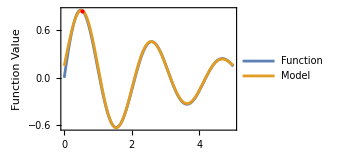

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x];
optimizationRegion=Interval[{0.,5.}];

bayesianOptimization=BayesianMaximization[objectiveFunction,optimizationRegion]

availableProperties=bayesianOptimization["Properties"]
evaluationHistory=bayesianOptimization["EvaluationHistory"]
explorationMethod=bayesianOptimization["Method"]
probabilisticModel=bayesianOptimization["PredictorFunction"]
nextConfiguration=bayesianOptimization["NextConfiguration"]
simultaneousProperties=bayesianOptimization[{"MaximumConfiguration","MaximumValue","Method"}]

Plot[
{objectiveFunction[x],probabilisticModel[x]},
{x,0,5},
Frame->{True,True,False,False},
FrameLabel->{"Configuration","Function Value"},
PlotLegends->{"Function","Model"},
ImageSize->250,
Epilog->{
Red,
PointSize[Large],
Point[{simultaneousProperties[[1]],simultaneousProperties[[2]]}]}]
```

code 7.30

(* The code conducts Bayesian minimization to find the minimum of the specified objective function f(x)=sin(3x)⋅Exp[−0.3 x] over the interval [0,5]. Through BayesianMinimization, the code retrieves various properties of the optimization process, including the estimated minimum configuration and value, as well as the history of evaluations made during the minimization. Additionally, the code visualizes the objective function and the probabilistic model on the same plot, allowing for an assessment of how well the function is modeled, particularly near the minimum: *)

{MinimumConfiguration,MinimumValue,EvaluationHistory,PredictorFunction,ObjectiveFunction,Method,Properties,NextConfiguration}

1.53416

-0.624942

{<|Configuration→2.60982,Value→0.45692|>,<|Configuration→0.431117,Value→0.845077|>,<|Configuration→3.79948,Value→-0.294261|>,<|Configuration→3.94693,Value→-0.203068|>,<|Configuration→3.30511,Value→-0.174789|>,<|Configuration→3.59844,Value→-0.332964|>,<|Configuration→3.57259,Value→-0.329272|>,<|Configuration→1.30185,Value→-0.468122|>,<|Configuration→4.89192,Value→0.197853|>,<|Configuration→1.77441,Value→-0.481045|>,<|Configuration→1.41913,Value→-0.586822|>,<|Configuration→1.62713,Value→-0.605025|>,<|Configuration→1.53416,Value→-0.627319|>,<|Configuration→0.156326,Value→0.431268|>,<|Configuration→1.65414,Value→-0.589883|>}

{1.55,MaxExpectedImprovement}

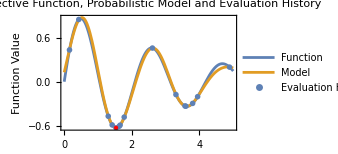

```mathematica
objectiveFunction[x_]:=Sin[3x]Exp[-0.3x];
minimizationRegion=Interval[{0,5}];

bayesianMinimization=BayesianMinimization[objectiveFunction,minimizationRegion];

availableProperties=bayesianMinimization["Properties"]
minimumConfiguration=bayesianMinimization["MinimumConfiguration"]
minimumValue=bayesianMinimization["MinimumValue"]
evaluationHistory=bayesianMinimization["EvaluationHistory"]//Normal
simultaneousProperties=bayesianMinimization[{"NextConfiguration","Method"}]
probabilisticModel=bayesianMinimization["PredictorFunction"];

Show[
Plot[
{objectiveFunction[x],probabilisticModel[{x}]},
{x,0,5},
Frame->{True,True,False,False},
FrameLabel->{"Configuration","Function Value"},
PlotLegends->{"Function","Model"},
ImageSize->250,
Epilog->{
Red,
PointSize[Large],
Point[{minimumConfiguration,minimumValue}]
}
],
ListPlot[
evaluationHistory,
PlotMarkers->"OpenMarkers",
PlotLegends->{"Evaluation History"}
],
PlotLabel->"Objective Function, Probabilistic Model\n and Evaluation History",
ImageSize->250
]
```

### Automated Hyperparameter Tuning with Mathematica

In machine learning, hyperparameter optimization is crucial for enhancing model performance, and it can be approached using methods like grid search, random search, and Bayesian optimization. Grid search evaluates every possible combination of a predefined set of hyperparameters, ensuring a thorough exploration of the space but often at a high computational cost. Random search, on the other hand, samples hyperparameters randomly from specified distributions, providing a more efficient alternative that can sometimes yield better results in less time. Bayesian optimization utilizes a probabilistic model to intelligently select hyperparameters based on past evaluations, aiming to find optimal solutions faster by focusing on more promising areas of the hyperparameter space. Each method has its advantages, and the choice depends on the specific constraints and goals of your project, such as computational resources and the sensitivity of model performance to hyperparameters. For grid search, you can use nested loops to iterate through combinations of hyperparameters. Similarly, for a random search, you can generate random samples of hyperparameters using Mathematica’s random number generation functions like RandomChoice. Bayesian optimization, facilitated by functions like BayesianMinimization/BayesianMaximization in Mathematica, employs probabilistic models to sequentially select hyperparameters, updating the model based on observed results to iteratively explore the parameter space efficiently.

code 7.31

(* The code is designed to generate synthetic data by adding noise to a mathematical function, train and evaluate neural network models using a grid search over different configurations of learning rates, neuron counts, and optimization methods. It aims to identify the optimal model parameters by evaluating performance metrics like Mean Squared Error (MSE) and R-Squared (RS). The code systematically tests various combinations of hyperparameters, trains the networks, and visually compares the best models’ predictions against the actual test data to assess their effectiveness. This process exemplifies practical applications of machine learning techniques, including hyperparameter tuning, performance evaluation, and result visualization: *)

{0.001,40,SGD,0.0248228,0.843833,NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3370  rounds:337  time:4.9s  examples/s:43761
data | ,,  training examples:601  validation examples:61  processed examples:215680  skipped examples:0
method | ,,  SGDoptimizer  batch size64CPU
round | ,,  loss:2.12×10^-2  res. mean sqr.:2.12×10^-2  res. r.b2:8.47×10^-1
validation | ,,  loss:2.48×10^-2  res. mean sqr.:2.48×10^-2  res. r.b2:8.44×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]}

{0.001,40,SGD,0.0248228,0.843833,NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3370  rounds:337  time:4.9s  examples/s:43761
data | ,,  training examples:601  validation examples:61  processed examples:215680  skipped examples:0
method | ,,  SGDoptimizer  batch size64CPU
round | ,,  loss:2.12×10^-2  res. mean sqr.:2.12×10^-2  res. r.b2:8.47×10^-1
validation | ,,  loss:2.48×10^-2  res. mean sqr.:2.48×10^-2  res. r.b2:8.44×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]}

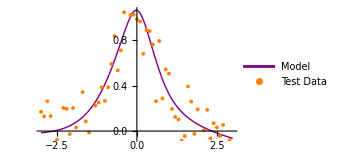

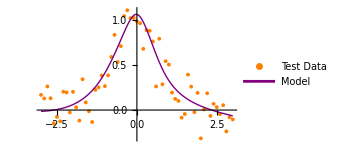

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];
testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

learningRates={0.001,0.05,0.1};
neuronCounts={10,30,40};
optimizationmethod={"ADAM","SGD","RMSProp"};

results=Table[
Module[
{net,trainedNet,validationMSE,validationRS},
net=NetChain[
{
50,Tanh,
neurons,Tanh,
1
}
];
trainedNet=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanSquare","RSquared"},
BatchSize->64,
LearningRate->learningRate,
Method->method,
TimeGoal->5
];

validationMSE=Values[trainedNet["ValidationMeasurements"]][[2]];validationRS=Values[trainedNet["ValidationMeasurements"]][[3]];

{learningRate,neurons,method,validationMSE,validationRS,trainedNet}
],
{learningRate,learningRates},
{neurons,neuronCounts},
{method,optimizationmethod}
];

sortedResultsByMSE=SortBy[Flatten[results,2],#[[4]]&];
sortedResultsByRS=SortBy[Flatten[results,2],#[[5]]&];

bestParametersByMSE=First[sortedResultsByMSE]
bestParametersByRS=Last[sortedResultsByRS]

bestModelByMSE=bestParametersByMSE[[6]]["TrainedNet"];
bestModelByRS=bestParametersByRS[[6]]["TrainedNet"];

plotModelByMSE=Plot[
bestModelByMSE[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plotModelByRS=Plot[
bestModelByRS[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plottestData=ListPlot[
List@@@testData,
PlotStyle->Orange,
PlotLegends->{"Test Data"}
];

Show[plotModelByMSE,plottestData,ImageSize->250]
Show[plottestData,plotModelByRS,ImageSize->250]
```

code 7.32

(* The goal of the code is to perform random search hyperparameter tuning for a neural network model. This involves generating synthetic datasets for training, validation, and testing, which simulate a Gaussian-modulated exponential function with noise. The code randomly explores different combinations of learning rates, neuron counts, and optimization methods to efficiently identify optimal configurations for the neural network. Each configuration is evaluated using metrics like Mean Squared Error (MSE) and R-Squared (RS). Ultimately, the code aims to find and visually compare the best neural network model against actual test data, assessing its ability to accurately predict and generalize from the given inputs. This approach allows for an efficient search across a potentially large parameter space, offering a practical alternative to the exhaustive grid search method, especially useful in scenarios with limited computational resources or when dealing with a high-dimensional hyperparameter space: *)

{0.001,10,RMSProp,0.0179095,0.879294,NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2912  rounds:291  time:5.0s  examples/s:37402
data | ,,  training examples:601  validation examples:61  processed examples:186368  skipped examples:0
method | ,,  RMSPropoptimizer  batch size64CPU
round | ,,  loss:2.31×10^-2  res. mean sqr.:2.31×10^-2  res. r.b2:8.38×10^-1
validation | ,,  loss:1.79×10^-2  res. mean sqr.:1.79×10^-2  res. r.b2:8.79×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]}

{0.001,10,RMSProp,0.0179095,0.879294,NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2912  rounds:291  time:5.0s  examples/s:37402
data | ,,  training examples:601  validation examples:61  processed examples:186368  skipped examples:0
method | ,,  RMSPropoptimizer  batch size64CPU
round | ,,  loss:2.31×10^-2  res. mean sqr.:2.31×10^-2  res. r.b2:8.38×10^-1
validation | ,,  loss:1.79×10^-2  res. mean sqr.:1.79×10^-2  res. r.b2:8.79×10^-1
 | 
-Graphics-  training set	-Graphics-  validation set | ]}

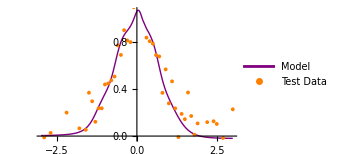

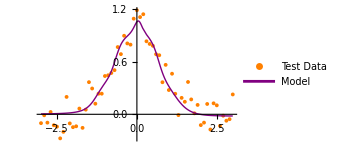

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];
testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

learningRates={0.001,0.05,0.1};
neuronCounts={10,30,40};
optimizationmethod={"ADAM","SGD","RMSProp"};

numTrials=5;

results=Table[
Module[
{learningRate,neurons,method,net,trainedNet,validationMSE,validationRS},
learningRate=RandomChoice[learningRates];
neurons=RandomChoice[neuronCounts];method=RandomChoice[optimizationmethod];

net=NetChain[
{
50,Tanh,
neurons,Tanh,
1
}
];
trainedNet=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanSquare","RSquared"},
BatchSize->64,
LearningRate->learningRate,
Method->method,
TimeGoal->5
];

validationMSE=Values[trainedNet["ValidationMeasurements"]][[2]];validationRS=Values[trainedNet["ValidationMeasurements"]][[3]];

{learningRate,neurons,method,validationMSE,validationRS,trainedNet}
],
{numTrials}
];

sortedResultsByMSE=SortBy[results,#[[4]]&];
sortedResultsByRS=SortBy[results,#[[5]]&];

bestParametersByMSE=First[sortedResultsByMSE]
bestParametersByRS=Last[sortedResultsByRS]

bestModelByMSE=bestParametersByMSE[[6]]["TrainedNet"];
bestModelByRS=bestParametersByRS[[6]]["TrainedNet"];

plotModelByMSE=Plot[
bestModelByMSE[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plotModelByRS=Plot[
bestModelByRS[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plottestData=ListPlot[
List@@@testData,
PlotStyle->Orange,
PlotLegends->{"Test Data"}
];

Show[plotModelByMSE,plottestData,ImageSize->250]
Show[plottestData,plotModelByRS,ImageSize->250]
```

code 7.33

(* The code encapsulates a complete workflow for developing and optimizing a neural network to approximate a Gaussian-modulated exponential function with added noise, representing typical real-world data scenarios. It starts by generating synthetic training, validation, and test datasets, then defines a neural network with two Tanh-activated hidden layers. The core of the code involves optimizing the learning rate using Bayesian minimization to minimize the mean squared error on the validation set, thereby tuning the model for better generalization. Post optimization, the model is trained with the best-found learning rate and evaluated against the test data. Finally, the results are visualized to assess the model’s predictive accuracy and fit, providing a comprehensive view of the model’s performance and the effectiveness of the chosen hyperparameter: *)

0.0429766

0.0263943

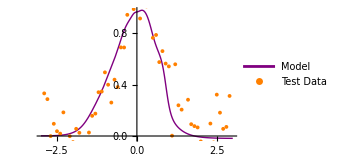

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];
testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

objectiveFunction[learningRate_]:=
Module[
{net,trainedNet,validationMSE},
net=NetChain[
{
50,Tanh,
30,Tanh,
1
}
];
trainedNet=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanSquare"},
BatchSize->64,
LearningRate->learningRate,
Method->"ADAM",
MaxTrainingRounds->5
];

validationMSE=Values[trainedNet["ValidationMeasurements"]][[2]];
validationMSE
];

optimizationResult=BayesianMinimization[
objectiveFunction,
Interval[{0.001,0.1}]
];

bestParameters=optimizationResult["MinimumConfiguration"]
bestMSE=optimizationResult["MinimumValue"]

evaluationHistory=optimizationResult["EvaluationHistory"]

finalModel=NetTrain[
NetChain[
{
50,Tanh,
30,Tanh,
1
}
],
trainingData,
All,
BatchSize->64,
LearningRate->bestParameters,
Method->"ADAM",
MaxTrainingRounds->5
];

finalModeltoplot=finalModel["TrainedNet"];

plotModel=Plot[
finalModeltoplot[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plottestData=ListPlot[
List@@@testData,
PlotStyle->Orange,
PlotLegends->{"Test Data"}
];

Show[plotModel,plottestData,ImageSize->250]
```

code 7.34

(* The enhanced code orchestrates a comprehensive process for developing a neural network tailored to model a Gaussian-modulated exponential function, incorporating noise to simulate real-world data. It features dynamic architecture configuration and employs Bayesian optimization to systematically explore and refine a range of hyperparameters - including learning rates, neuron counts, and optimizer types - to minimize validation mean squared error (MSE). The optimization is conducted in two stages to efficiently pinpoint optimal settings, which are then used to train the final model. This model is rigorously evaluated against test data and visually assessed through plots that compare its predictions with actual data, demonstrating its predictive accuracy and generalization capabilities: *)

{{0.00001,30,5,SGD},{0.001,30,30,SGD},{0.01,30,10,SGD},{0.01,40,10,RMSProp},{0.00001,40,10,RMSProp},{0.00001,30,30,ADAM},{0.001,40,30,RMSProp},{0.00001,30,30,ADAM},{0.1,30,10,RMSProp},{0.1,40,10,RMSProp},{0.1,30,30,RMSProp},{0.0001,40,5,SGD},{0.00001,40,30,RMSProp},{0.001,30,5,ADAM},{0.00001,30,30,RMSProp},{0.001,40,10,ADAM},{0.00001,30,30,SGD},{0.0001,30,30,RMSProp},{0.00001,40,10,ADAM},{0.00001,30,10,RMSProp},{0.01,30,5,RMSProp},{0.01,30,30,RMSProp},{0.01,40,30,SGD},{0.001,40,10,RMSProp},{0.001,40,5,ADAM},{0.01,40,5,ADAM},{0.0001,30,5,RMSProp},{0.01,30,10,RMSProp},{0.1,40,10,RMSProp},{0.0001,40,30,SGD},{0.01,40,10,SGD},{0.1,40,10,SGD},{0.001,30,5,ADAM},{0.1,40,10,ADAM},{0.0001,30,10,RMSProp},{0.0001,40,5,SGD},{0.00001,30,10,RMSProp},{0.0001,30,10,SGD},{0.01,40,30,SGD},{0.1,30,10,SGD},{0.00001,40,30,ADAM},{0.0001,40,30,SGD},{0.1,40,10,SGD},{0.1,30,10,SGD},{0.00001,30,30,RMSProp},{0.0001,30,30,RMSProp},{0.00001,40,10,RMSProp},{0.01,30,5,SGD},{0.0001,30,5,RMSProp},{0.01,40,5,RMSProp}}

{0.001,40,30,RMSProp}

0.0240789

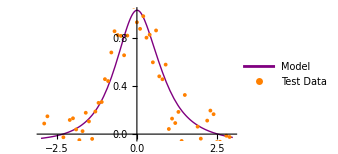

```mathematica
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];
testData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

objectiveFunction[{learningRate_,neurons1_,neurons2_,method_}]:=Module[
{net,trainedNet,validationMSE},
net=NetChain[
{
neurons1,Tanh,
neurons2,Tanh,
1
}
];
trainedNet=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanSquare"},
BatchSize->64,
LearningRate->learningRate,
Method->method,
MaxTrainingRounds->10
];
validationMSE=Values[trainedNet["ValidationMeasurements"]][[2]];
validationMSE
];

learningRates={0.00001,0.0001,0.001,0.01,0.1};
numberOfNeuronsLayer1={30,40};
numberOfNeuronsLayer2={5,10,30};
optimizers={"ADAM","SGD","RMSProp"};

conf=Table[
{
RandomChoice[learningRates],
RandomChoice[numberOfNeuronsLayer1],
RandomChoice[numberOfNeuronsLayer2],
RandomChoice[optimizers]
},
50]

optimizationResult1=BayesianMinimization[
objectiveFunction,
conf,
Method->"MaxExpectedImprovement",
MaxIterations->5
];

evaluationHistory1=optimizationResult1["EvaluationHistory"]

optimizationResult2=BayesianMinimization[
objectiveFunction,
conf,
InitialEvaluationHistory->evaluationHistory1,
Method->"MaxExpectedImprovement"
];

evaluationHistory2=optimizationResult2["EvaluationHistory"]
bestParameters=optimizationResult2["MinimumConfiguration"]
bestMSE=optimizationResult2["MinimumValue"]

finalModel=NetTrain[
NetChain[
{
bestParameters[[2]],Tanh,
bestParameters[[3]],Tanh,
1
}
],
trainingData,
All,
BatchSize->64,
LearningRate->bestParameters[[1]],
Method->bestParameters[[4]],
MaxTrainingRounds->10
];

finalModeltoplot=finalModel["TrainedNet"];

plotModel=Plot[
finalModeltoplot[x],
{x,-3,3},
PlotStyle->{Purple,Thick},
PlotLegends->{"Model"}
];

plottestData=ListPlot[
List@@@testData,
PlotStyle->Orange,
PlotLegends->{"Test Data"}
];

Show[plotModel,plottestData,ImageSize->250]
```